## GME Lukin-Structure

NOTE: Some calculations are made using ParallelDo or ParallelTable, that use several cores of the CPU.

### Parameters

```mathematica
T0=AbsoluteTime[];
SetDirectory[NotebookDirectory[]];
(**************************************************)
(*parameters of the structure*)
a=1.0;(*lattice parameter*)
we=0.01;(*parameter used in the searching of the guided modes*)
rs=0.0833 ; (*radio of the outer holes *)
rl=0.15; (*radio of the inner holes*)
l=0.4; (* distance of the inner holes to the center of the unit cell*)
d=0.25 ; (*slab width*)
ex1=1; (*permittivity of the upper layer*)
ex3=1; (*permittivity of the lower layer*)
es=10.5625; (*permittivity of the slab backfground*)
er=1.0; (*permi+ttivity of the holes in the slab*)
S=Sqrt[3]/2*a^2; (*area of the unit cell*)
(*parameters of the calculation*)
gx=gy=9;(*Must be integer, give a idea of the basis size of the in-plane reciprocal lattice vector*)
Ng=3;(*Must be integer, number of guided modes for each g*)
sig=1;(*Must be integer*)
(**************************************************)
kx=2π/a* (1/Sqrt[3]); ky=2π/a* (1/3);(*Coordinates of the K point*)
(**************************************************)
```

```mathematica
Clear[coef,coef1, coef2,G,Cet,epsm,NTE,A2,B2,A3,NTM,C2,D2,C3,W1,W2,W3,X1,X2,X3,Y1,Y2,Y3,Z1,Z2,Z3];
```

```mathematica
Norm[{1/√3,1}]
```

2/(√3)

#### Basis of PW, circular cutoff

Here, the program select the set of G that will use to build up the basis of guided modes. It use a circular cutoff to chose the set, it is all the G vectos that satisfie the condition G ≤Gmax= gx* (4π)/(√3 a)

```mathematica
gg[n_,m_]:=2 π/a N[n*{1/√3,1}+m*{-1/√3,1}];gr[n_,m_,θ_]:=2π/a {{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}.(n*{1/√3,1}+m*{-1/√3,1});Gmax=Norm[gg[gx,0]];
Gg={};
Do[ Do[If[Norm[gg[i,j]]≤Gmax,AppendTo[Gg,{i,j}]],{i,-2gx,2gx}],{j,-2gy,2gy}];
G[m_]:=G[m]=N[gg[Gg⟦m,1⟧,Gg⟦m,2⟧]];
lg=Length[Gg];
gmax=Max[Gg⟦All,1⟧];
Print["The set of G vectors have ", lg, " elements"]
```

The set of G vectors have 301 elements

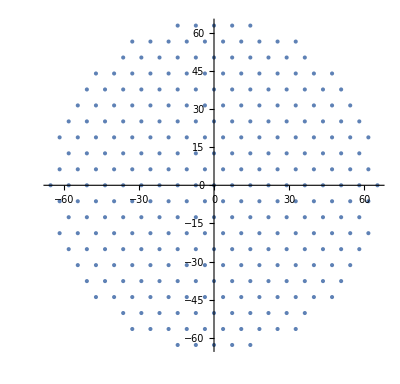

```mathematica
ListPlot[Table[G[m],{m,lg}],AspectRatio->Automatic] 
(*Each point in the plot represent a G vector we will use to build up the guided modes*)
```

### Permitivity Structure

Here, we define functions to describe the structure of the dielectric media. First, we define a piecewise function with the exact value of the permittivity at any r in the unit cell. Second, we  calculate the Fourier coefficients to expand the dielectric permittivity in the plane and construct the matrix elements η_(G-G')associated with the structure of the unit cell.

#### Analytic Dielectric Function

```mathematica
(*Mesh in the hexagonal unit cell to evaluated the permittivity, fields, Green functions or any other function of the position*)
Rlist=Flatten[Table[N[{xx,yy}],{xx,-Sqrt[3]/3,Sqrt[3]/3,(2/3Sqrt[3]/3)/50},{yy,-0.5,0.5,1/50}],1]; (*Mesh in a rectangular area*)
RHex={};(*Mesh in a hexagonal (unit cell) area*)
Do[{xX,yY}=Rlist⟦i⟧;
If[(Abs[xX]≤ Sqrt[3]/6 && Abs[yY] <=0.5),AppendTo[RHex,{xX,yY}],If[Abs[xX]≥  Sqrt[3]/6&& Abs[yY]≤  -Sqrt[3]Abs[xX]+1,AppendTo[RHex,{xX,yY}]]],{i,1,Length[Rlist]}];
(*Below, we define the analytical piecewise dielectric function in the unit cell*)
Eps[x_,y_]:=es-If[(Norm[Abs[{x,y}]-{Sqrt[3]/3,0}]≤ rs||Norm[Abs[{x,y}]-{Sqrt[3]/6,0.5}]≤ rs||Norm[Abs[{x,y}]-{0,0.5}]≤ rl||Norm[Abs[{x,y}]-{Sqrt[3]/4,0.25}]≤ rl),es-er,0]
```

```mathematica
EpsList=Table[{RHex⟦i,1⟧,RHex⟦i,2⟧,Eps[RHex⟦i,1⟧,RHex⟦i,2⟧]},{i,1,Length[RHex]}]; (*Evaluating the dielectric function in the unit cell mesh*)
```

```mathematica
(*We define the plot of the dielectric function, to be used before in some graphs*)
EpsGrap=ListDensityPlot[EpsList,ColorFunction->"GrayTones",PlotStyle-> Opacity[0.1]];
EpsGrapFull=ListDensityPlot[EpsList,ColorFunction->"GrayTones"];
```

#### Coefficients of dielectric structure

```mathematica
II[Gx_,Gy_]:=II[Gx,Gy]=NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,-√(rl^2-(0.5 a-l+yy)^2),0}],{yy,-(0.5 a-l+rl),0}]+NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,-√(rl^2-(0.5 a-l-yy)^2),0}],{yy,0,(0.5 a-l+rl)}]+NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,0,√(rl^2-(0.5 a-l+yy)^2)}],{yy,-(0.5 a-l+rl),0}]+NIntegrate[Integrate[Exp[ⅈ {Gx,Gy}.{xx,yy}],{xx,0,√(rl^2-(0.5 a-l-yy)^2)}],{yy,0,(0.5 a-l+rl)}];
coef1[n_,m_]:=coef1[n,m]=(er-es)/(√3 a^2/2)*If[Norm[gg[n,m]]==0, 2π rs^2,2 π rs BesselJ[1, rs Norm[gg[n,m]]]/Norm[gg[n,m]](Exp[ⅈ gg[n,m].{√3 a/3,0}]+Exp[ⅈ gg[n,m].{-√3 a/3,0}])];
coef2[n_,m_]:=coef2[n,m]=(er-es)/(√3 a^2/2)(Exp[ⅈ gg[n,m].{0,-0.5*a}]*II[gg[n,m][[1]],gg[n,m][[2]]]+Exp[ⅈ gg[n,m].{-√3 a/4,a/4}]II[gr[n,m,π/3][[1]],gr[n,m,π/3][[2]]]+Exp[ⅈ gg[n,m].{√3 a/4,a/4}]II[gr[n,m,-π/3][[1]],gr[n,m,-π/3][[2]]]);
coef[n_,m_]:=coef[n,m]=coef[-n,-m]=coef[m,n]=If[Norm[gg[n,m]]==0, es+coef1[n,m]+coef2[n,m],coef1[n,m]+coef2[n,m]];
```

```mathematica
Coef=Import["Coef-Eps-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat"];
```

#### Matrix for permitivity coeffients

```mathematica
Mets=Import["Matrix-Eta-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];
Coefinv=Table[Mets⟦(Length[Mets]+1)/2,i⟧,{i,Length[Mets]}];
Cet[l_,m_,mp_]:=Cet[l,m,mp]=N[If[l==1,N[(1/ex1)]*IdentityMatrix[Length[Gg]]⟦m,mp⟧,If[l==2,Mets⟦m,mp⟧,If[l==3,N[(1/ex3)]*IdentityMatrix[Length[Gg]]⟦m,mp⟧]]]];
epsm[j_]:=epsm[j]=N[(2/(a a Sqrt[3])) If[j==1,ex1 a a Sqrt[3]/2,If[j==2,es*(a a Sqrt[3]/2-3*II[0,0]-2 π rs^2)+(3*II[0,0]+2 π rs^2)er,ex3 a a Sqrt[3]/2]]];
```

#### Plotting the expansion of permitivity

```mathematica
epsop[x_,y_]:=Chop[Sum[Coef⟦2*gmax+1+Gg⟦i,1⟧,2gmax +1+Gg⟦i,2⟧⟧ Exp[N[I G[i].{x,y}]],{i,Length[Gg]}]];
eps3D[x_,y_,z_]:=If[Abs[z]<=0.5d,epsop[x,y],1];
epsinvop[x_,y_]:=Chop[Sum[Coefinv⟦i⟧ Exp[N[I G[i].{x,y}]],{i,Length[Gg]}]];
```

```mathematica
listaepsop=ParallelTable[{x,y,epsop[x,y]},{x,-2Sqrt[3]/3,2Sqrt[3]/3,0.01},{y,-0.5,0.5,0.01}];
```

```mathematica
listaepsinvop=ParallelTable[{x,y,epsinvop[x,y]},{x,-2Sqrt[3]/3,2Sqrt[3]/3,0.01},{y,-0.5,0.5,0.01}];
```

```mathematica
ListDensityPlot[Flatten[listaepsinvop,1],AspectRatio->Automatic, PlotLegends-> Automatic]
(*ListDensityPlot[Flatten[listaEpsInvop,1],AspectRatio->Automatic, PlotLegends-> Automatic]*)
```

-Graphics-

```mathematica
Show[{ListDensityPlot[Flatten[listaepsop,1],ColorFunction->"TemperatureMap",FrameTicksStyle->Directive[Black,20],PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic,AspectRatio->Automatic],ListPlot[{{{-2Sqrt[3]/3,0},{2Sqrt[3]/3,0}},{{0,0}},{{0,-0.5},{0,0.5}}},Joined->True]}]
```

-Graphics-

### Init Structure

```mathematica
X[j_,g_,w_]:=N[Sqrt[g^2-epsm[j] (w^2)]];
qg[g_,w_]:=N[Sqrt[epsm[2] (w^2)-g^2]];
TEsigp[g_,w_]:=N[qg[g,w] Sin[qg[g,w] 0.5 d]-X[1,g,w] Cos[qg[g,w] 0.5 d]];
TEsigm[g_,w_]:=N[qg[g,w] Cos[qg[g,w] 0.5 d]+X[1,g,w] Sin[qg[g,w] 0.5 d]];
TMsigp[g_,w_]:=N[(qg[g,w]/epsm[2]) Cos[qg[g,w] 0.5 d]+(X[1,g,w]/epsm[1]) Sin[qg[g,w] 0.5 d]];
TMsigm[g_,w_]:=N[(qg[g,w]/epsm[2]) Sin[qg[g,w] 0.5 d]-(X[1,g,w]/epsm[1]) Cos[qg[g,w] 0.5 d]];
If[sig==1,If[Mod[Ng,2]==0,Ngte=Ngtm=Ng/2,Ngte=0.5 (Ng+1);
Ngtm=0.5 (Ng-1)],If[Mod[Ng,2]==0,Ngte=Ngtm=Ng/2,Ngte=0.5 (Ng-1);
Ngtm=0.5 (Ng+1)]];
eg[g_]:=Normalize[{-g[[2]],g[[1]]}];
A2p[g_,w_]:=N[0.5 (qg[g,w]-I X[1,g,w]) Exp[I qg[g,w] 0.5 d]/qg[g,w]];
B2p[g_,w_]:=N[0.5 (qg[g,w]+I X[1,g,w]) Exp[-I qg[g,w] 0.5 d]/qg[g,w]];
A3p[g_,w_]:=N[0.5 (qg[g,w] (X[3,g,w]-X[1,g,w]) Cos[qg[g,w] d]+(qg[g,w]^2+X[1,g,w] X[3,g,w]) Sin[qg[g,w] d])/(qg[g,w] X[3,g,w])];
NTE[g_,w_]:=NTE[g,w]=Chop[Sqrt[1/(((X[1,g,w]^2+g^2)/(2 X[1,g,w]))+(((X[3,g,w]^2+g^2) (Norm[A3p[g,w]]^2))/(2 X[3,g,w]))+d ((g^2+qg[g,w]^2) (Norm[A2p[g,w]]^2+Norm[B2p[g,w]]^2)+((g^2-qg[g,w]^2) (Conjugate[A2p[g,w]] B2p[g,w]+Conjugate[B2p[g,w]] A2p[g,w]) Sin[qg[g,w] d]/(qg[g,w] d))))]];
A2[g_,w_]:=A2[g,w]=NTE[g,w] A2p[g,w];
B2[g_,w_]:=B2[g,w]=NTE[g,w] B2p[g,w];
A3[g_,w_]:=A3[g,w]=NTE[g,w] A3p[g,w];
C2p[g_,w_]:=((qg[g,w]/epsm[2])-I (X[1,g,w]/epsm[1])) Exp[I qg[g,w] d/2]/(2 (qg[g,w]/epsm[2]));
D2p[g_,w_]:=((qg[g,w]/epsm[2])+I (X[1,g,w]/epsm[1])) Exp[-I qg[g,w] d/2]/(2 (qg[g,w]/epsm[2]));
C3p[g_,w_]:=((qg[g,w]/epsm[2]) ((X[3,g,w]/epsm[3])-(X[1,g,w]/epsm[1])) Cos[qg[g,w] d]+((qg[g,w]/epsm[2])^2+(X[1,g,w]/epsm[1]) (X[3,g,w]/epsm[3])) Sin[qg[g,w] d])/(2 (qg[g,w]/epsm[2]) (X[3,g,w]/epsm[3]));
NTM[g_,w_]:=NTM[g,w]=Chop[Sqrt[1/((1/(2 X[1,g,w]))+((Norm[C3p[g,w]]^2)/(2 X[3,g,w]))+d (Norm[C2p[g,w]]^2+Norm[D2p[g,w]]^2+(Conjugate[C2p[g,w]] D2p[g,w]+Conjugate[D2p[g,w]] C2p[g,w]) Sin[qg[g,w] d]/(qg[g,w] d)))]];
C2[g_,w_]:=C2[g,w]=NTM[g,w] C2p[g,w];
D2[g_,w_]:=D2[g,w]=NTM[g,w] D2p[g,w];
C3[g_,w_]:=C3[g,w]=NTM[g,w] C3p[g,w];
I1[g_,gp_,w_,wp_]:=(X[1,g,w]+X[1,gp,wp])^(-1);
I2p[g_,gp_,w_,wp_]:=Sin[(qg[g,w]+qg[gp,wp]) d/2]/((qg[g,w]+qg[gp,wp])/2);
I2m[g_,gp_,w_,wp_]:=If[(qg[g,w]-qg[gp,wp])==0,d,Sin[(qg[g,w]-qg[gp,wp]) d/2]/((qg[g,w]-qg[gp,wp])/2)];
I3[g_,gp_,w_,wp_]:=(X[3,g,w]+X[3,gp,wp])^(-1);
q[j_,g_,w_]:=N[Sqrt[epsm[j] (w^2)-g^2]];
Mte21[g_,w_]:=N[(1/(2 q[2,g,w]))*{{(q[2,g,w]+q[1,g,w]) Exp[0.5I q[2,g,w] d],(q[2,g,w]-q[1,g,w]) Exp[0.5I q[2,g,w] d]},{(q[2,g,w]-q[1,g,w]) Exp[-0.5I q[2,g,w] d],(q[2,g,w]+q[1,g,w]) Exp[-0.5I q[2,g,w] d]}}];
Mte32[g_,w_]:=N[(0.5/ q[3,g,w])*{{(q[3,g,w]+q[2,g,w]) Exp[0.5I q[2,g,w] d],(q[3,g,w]-q[2,g,w]) Exp[-0.5I q[2,g,w] d]},{(q[3,g,w]-q[2,g,w]) Exp[0.5I q[2,g,w] d],(q[3,g,w]+q[2,g,w]) Exp[-0.5I q[2,g,w] d]}}];
Mte31[g_,w_]:=N[(0.25/(q[2,g,w]q[3,g,w])){{(q[2,g,w]+q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]-q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[-I q[2,g,w] d],(q[2,g,w]-q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]+q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[-I q[2,g,w] d]},{(q[2,g,w]+q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]-q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[-I q[2,g,w] d],(q[2,g,w]-q[1,g,w])(q[3,g,w]-q[2,g,w])Exp[I q[2,g,w] d]+(q[2,g,w]+q[1,g,w])(q[3,g,w]+q[2,g,w])Exp[-I q[2,g,w] d]}}];
X1l=N[1/Sqrt[epsm[1]]];
W1l[g_,w_]:=-(Mte31[g,w][[1,2]]/Mte31[g,w][[1,1]]) X1l;
W2l[g_,w_]:=Mte21[g,w][[1,1]] W1l[g,w]+Mte21[g,w][[1,2]] X1l;
X2l[g_,w_]:=Mte21[g,w][[2,1]] W1l[g,w]+Mte21[g,w][[2,2]] X1l;
W3l=N[0];
X3l[g_,w_]:=Mte32[g,w][[2,1]] W2l[g,w]+Mte32[g,w][[2,2]] X2l[g,w];
W3u=N[1/Sqrt[epsm[3]]];
X3u[g_,w_]:=(Mte31[g,w][[2,1]]/Mte31[g,w][[1,1]]) W3u;
W1u[g_,w_]:=W3u/Mte31[g,w][[1,1]];
X1u=N[0];
W2u[g_,w_]:=Mte21[g,w][[1,1]] W1u[g,w];
X2u[g_,w_]:=Mte21[g,w][[2,1]] W1u[g,w];
W1[g_,w_,j_]:=W1[g,w,j]=If[j==1,W1l[g,w],If[j==3,W1u[g,w]]];
W2[g_,w_,j_]:=W2[g,w,j]=If[j==1,W2l[g,w],If[j==3,W2u[g,w]]];
W3[g_,w_,j_]:=W3[g,w,j]=If[j==1,W3l,If[j==3,W3u]];
X1[g_,w_,j_]:=X1[g,w,j]=If[j==1,X1l,If[j==3,X1u]];
X2[g_,w_,j_]:=X2[g,w,j]=If[j==1,X2l[g,w],If[j==3,X2u[g,w]]];
X3[g_,w_,j_]:=X3[g,w,j]=If[j==1,X3l[g,w],If[j==3,X3u[g,w]]];
Mtm21[g_,w_]:=N[(0.5/(q[2,g,w]/epsm[2]))*{{((q[2,g,w]/epsm[2])+(q[1,g,w]/epsm[1])) Exp[0.5I q[2,g,w] d],((q[2,g,w]/epsm[2])-(q[1,g,w]/epsm[1])) Exp[0.5I q[2,g,w] d]},{((q[2,g,w]/epsm[2])-(q[1,g,w]/epsm[1])) Exp[-0.5I q[2,g,w] d],((q[2,g,w]/epsm[2])+(q[1,g,w]/epsm[1])) Exp[-0.5I q[2,g,w] d]}}];
Mtm32[g_,w_]:=N[(0.5/(q[3,g,w]/epsm[3]))*{{((q[3,g,w]/epsm[3])+(q[2,g,w]/epsm[2])) Exp[0.5I q[2,g,w] d],((q[3,g,w]/epsm[3])-(q[2,g,w]/epsm[2])) Exp[-0.5I q[2,g,w] d]},{((q[3,g,w]/epsm[3])-(q[2,g,w]/epsm[2])) Exp[0.5I q[2,g,w] d],((q[3,g,w]/epsm[3])+(q[2,g,w]/epsm[2])) Exp[-0.5I q[2,g,w] d]}}];
Mtm31[g_,w_]:=N[(0.25/(q[2,g,w]q[3,g,w]/(epsm[2]epsm[3]))){{(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d],(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d]},{(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d],(q[2,g,w]/epsm[2]-q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]-q[2,g,w]/epsm[2])Exp[I q[2,g,w] d]+(q[2,g,w]/epsm[2]+q[1,g,w]/epsm[1])(q[3,g,w]/epsm[3]+q[2,g,w]/epsm[2])Exp[-I q[2,g,w] d]}}];
Z1l=N[1];
Y1l[g_,w_]:=-(Mtm31[g,w][[1,2]]/Mtm31[g,w][[1,1]]) Z1l;
Y2l[g_,w_]:=Mtm21[g,w][[1,1]] Y1l[g,w]+Mtm21[g,w][[1,2]] Z1l;
Z2l[g_,w_]:=Mtm21[g,w][[2,1]] Y1l[g,w]+Mtm21[g,w][[2,2]] Z1l;
Y3l=N[0];
Z3l[g_,w_]:=Mtm32[g,w][[2,1]] Y2l[g,w]+Mtm32[g,w][[2,2]] Z2l[g,w];
Y3u=N[1];
Z3u[g_,w_]:=(Mtm31[g,w][[2,1]]/Mtm31[g,w][[1,1]]) Y3u;
Y1u[g_,w_]:=Y3u/Mtm31[g,w][[1,1]];
Z1u=N[0];
Y2u[g_,w_]:=Mtm21[g,w][[1,1]] Y1u[g,w];
Z2u[g_,w_]:=Mtm21[g,w][[2,1]] Y1u[g,w];
Y1[g_,w_,j_]:=Y1[g,w,j]=If[j==1,Y1l[g,w],If[j==3,Y1u[g,w]]];
Y2[g_,w_,j_]:=Y2[g,w,j]=If[j==1,Y2l[g,w],If[j==3,Y2u[g,w]]];
Y3[g_,w_,j_]:=Y3[g,w,j]=If[j==1,Y3l,If[j==3,Y3u]];
Z1[g_,w_,j_]:=Z1[g,w,j]=If[j==1,Z1l,If[j==3,Z1u]];
Z2[g_,w_,j_]:=Z2[g,w,j]=If[j==1,Z2l[g,w],If[j==3,Z2u[g,w]]];
Z3[g_,w_,j_]:=Z3[g,w,j]=If[j==1,Z3l[g,w],If[j==3,Z3u[g,w]]];
Ir1p[g_,gp_,w_,wp_]:=(X[1,g,w]+I q[1,gp,wp])^(-1);
Ir1m[g_,gp_,w_,wp_]:=(X[1,g,w]-I q[1,gp,wp])^(-1);
Ir2p[g_,gp_,w_,wp_]:=Sin[0.5(qg[g,w]+q[2,gp,wp]) d]/(0.5(qg[g,w]+q[2,gp,wp]));
Ir2m[g_,gp_,w_,wp_]:=If[(qg[g,w]-q[2,gp,wp])==0,d,Sin[0.5(qg[g,w]-q[2,gp,wp]) d]/(0.5(qg[g,w]-q[2,gp,wp]))];
Ir3p[g_,gp_,w_,wp_]:=(X[3,g,w]+I q[3,gp,wp])^(-1);
Ir3m[g_,gp_,w_,wp_]:=(X[3,g,w]-I q[3,gp,wp])^(-1);
```

### Bands

Here, we define the routines to calculate the band structures and modes of the photonic crystal slab. There are three routines, the first one is the sames as in the 1-GME.nb; the second, we have a routine that use saved GME-matrix elements for calculate the eigenproblem at K or K’; and finally, the third (fourth) routine use the saved GME-matrix elements to solve the eigenproblem at point k_1(k_1’) close to the Dirac cone at K(K’).

NOTE: The eigenvalues, eigenvectors and spatial modes of the fields are sort by frequency from the biggest one to the lowest. So, the index 1 is associated with the biggest eigenvalue and the largest index is associated with the lowest eigenvalue.

#### Bands Modules

WV Completa

```mathematica
WV[k0_,nb_,wv_]:=Module[{k=k0},
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];Htete[mu_,nu_]:=N[Chop[(solTE⟦mu,2⟧^2) (solTE⟦nu,2⟧^2) (eg[gs⟦solTE⟦mu,1⟧⟧].eg[gs⟦solTE⟦nu,1⟧⟧]) ((epsm[1]^2) Cet[1,solTE⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] NTE[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] I1[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]+(epsm[3]^2) Cet[3,solTE⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] A3[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] I3[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]+(epsm[2]^2) Cet[2,solTE⟦mu,1⟧,solTE⟦nu,1⟧] ((Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]+Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2m[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]+(Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]+Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2p[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTE⟦nu,2⟧]))]];Htmtm[mu_,nu_]:=N[Chop[Cet[1,solTM⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] NTM[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I1[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧]+Cet[3,solTM⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] C3[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I3[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧]+Cet[2,solTM⟦mu,1⟧,solTM⟦nu,1⟧] ((Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]+Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) (qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] qg[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I2m[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧]+(Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]+Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) (-qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] qg[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] (Normalize[gs⟦solTM⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧])+Norm[gs⟦solTM⟦mu,1⟧⟧] Norm[gs⟦solTM⟦nu,1⟧⟧]) I2p[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTM⟦nu,2⟧])]];Htetm[mu_,nu_]:=N[Chop[(solTE⟦mu,2⟧^2) (eg[gs⟦solTE⟦mu,1⟧⟧].Normalize[gs⟦solTM⟦nu,1⟧⟧]) (-epsm[1] Cet[1,solTE⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] NTM[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] X[1,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] I1[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]+epsm[3] Cet[3,solTE⟦mu,1⟧,solTM⟦nu,1⟧] Conjugate[A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] C3[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] X[3,Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] I3[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]+I epsm[2] Cet[2,solTE⟦mu,1⟧,solTM⟦nu,1⟧] qg[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧] ((-Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]+Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) I2m[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]+(Conjugate[A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] D2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]-Conjugate[B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧]] C2[Norm[gs⟦solTM⟦nu,1⟧⟧],solTM⟦nu,2⟧]) I2p[Norm[gs⟦solTE⟦mu,1⟧⟧],Norm[gs⟦solTM⟦nu,1⟧⟧],solTE⟦mu,2⟧,solTM⟦nu,2⟧]))]];Htmte[mu_,nu_]:=N[Chop[(solTE⟦nu,2⟧^2) (Normalize[gs⟦solTM⟦mu,1⟧⟧].eg[gs⟦solTE⟦nu,1⟧⟧]) (-epsm[1] Cet[1,solTM⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] NTE[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] X[1,Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] I1[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]+epsm[3] Cet[3,solTM⟦mu,1⟧,solTE⟦nu,1⟧] Conjugate[C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] A3[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I3[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]-I epsm[2] Cet[2,solTM⟦mu,1⟧,solTE⟦nu,1⟧] qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] ((-Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]+Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2m[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]+(Conjugate[D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] A2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]-Conjugate[C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]] B2[Norm[gs⟦solTE⟦nu,1⟧⟧],solTE⟦nu,2⟧]) I2p[Norm[gs⟦solTM⟦mu,1⟧⟧],Norm[gs⟦solTE⟦nu,1⟧⟧],solTM⟦mu,2⟧,solTE⟦nu,2⟧]))]];
NeTe=Length[solTE];
NeTm=Length[solTM];
Do[MH[m,n]=Htmtm[m,n],{m,NeTm},{n,NeTm}];Do[MH[m+NeTm,n+NeTm]=Htete[m,n],{m,NeTe},{n,NeTe}];Do[MH[m,n+NeTm]=Htmte[m,n],{m,NeTm},{n,NeTe}];Do[MH[m+NeTm,n]=Htetm[m,n],{m,NeTe},{n,NeTm}];MM=Table[MH[i,j],{i,NeTe+NeTm},{j,NeTe+NeTm}];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

WV reading a symmetric point k

```mathematica
WVrec[k0_,nb_,wv_]:=Module[{k=k0},
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];
NeTe=Length[solTE];
NeTm=Length[solTM];
MM=Import["MatrixGME-kx_"<>ToString[k0⟦1⟧]<>"-ky_"<>ToString[k0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

WV reading a symmetric point k

```mathematica
WVrec[k0_,nb_,wv_]:=Module[{k=k0},
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];
NeTe=Length[solTE];
NeTm=Length[solTM];
MM=Import["MatrixGME-kx_"<>ToString[k0⟦1⟧]<>"-ky_"<>ToString[k0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

WV reading k_1

```mathematica
k1=Import["k1-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat"];
```

```mathematica
WVreck[nk0_,nb_,wv_]:=Module[{nk=nk0},
k=If[nk==2,k2,If[nk==3,k3,k1]];
Stringk=If[nk==2,"k2",If[nk==3,"k3","k1"]];
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];
NeTe=Length[solTE];
NeTm=Length[solTM];
MM=Import["MatrixGME-"<>Stringk<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

WV reading k_1’

```mathematica
kp1=Import["kp1-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat"];
```

```mathematica
WVreckp[nk0_,nb_,wv_]:=Module[{nk=nk0},
k=If[nk==2,kp2,If[nk==3,kp3,kp1]];
Stringk=If[nk==2,"kp2",If[nk==3,"kp3","kp1"]];
solTE={};solTM={};gs=Table[k+G[m],{m,lg}];
Do[g=Norm[gs⟦i⟧];
wmin=N[g/Sqrt[epsm[2]]+(10^-10)];wmax=N[g/Max[{Sqrt[epsm[1]],Sqrt[epsm[3]]}]-(10^-10)];dw=(wmax-wmin)/If[Round[(wmax-wmin)/we]<2,2,Round[(wmax-wmin)/we]];semte={}; semtm={};If[Ngte!=0,Do[If[Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=0&&Sign[If[sig==1,TEsigp[g,w],TEsigm[g,w]]]!=Sign[If[sig==1,TEsigp[g,w+dw],TEsigm[g,w+dw]]],AppendTo[semte,w];If[Length[semte]>=Ngte,Break[]]],{w,wmin,wmax-dw,dw}]];If[Ngtm!=0,Do[If[Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=0&&Sign[If[sig==1,TMsigp[g,w],TMsigm[g,w]]]!=Sign[If[sig==1,TMsigp[g,w+dw],TMsigm[g,w+dw]]],AppendTo[semtm,w];If[Length[semtm]>=Ngtm,Break[]]],{w,wmin,wmax-dw,dw}]];If[semte!={},sol1TE=wf/.FindRoot[If[sig==1,TEsigp[g,wf],TEsigm[g,wf]]==0,{wf,semte}];Do[AppendTo[solTE,{i,Chop[sol1TE]⟦j⟧}],{j,Length[Chop[sol1TE]]}]];If[semtm!={},sol1TM=wf/.FindRoot[If[sig==1,TMsigp[g,wf],TMsigm[g,wf]]==0,{wf,semtm}];Do[AppendTo[solTM,{i,Chop[sol1TM]⟦j⟧}],{j,Length[Chop[sol1TM]]}]],{i,lg}];
NeTe=Length[solTE];
NeTm=Length[solTM];
MM=Import["MatrixGME-"<>Stringk<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"];If[HermitianMatrixQ[Chop[SetPrecision[MM,10]]]==False,Print["Non-Hermitian Matrix"];Abort[]];Eigenproblem=Eigensystem[Chop[MM],-nb];frecs=a*Sqrt[N[Eigenproblem⟦1⟧]]/(2 Pi);CoefMM=N[Eigenproblem⟦2⟧];Dxx={};Dyy={};Dzz={};
Hxx={};
Hyy={};
Hzz={};
Do[vkf=CoefMM⟦in⟧;HgTEx[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;HgTEy[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],-NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTEz[x_,y_,z_,mu_]:=Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}]*If[z>0.5d,A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] I Norm[gs⟦solTE⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]];DgTEx[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE[[mu,2]]] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦1⟧;DgTEy[x_,y_,z_,mu_]:=I Exp[I gs⟦solTE⟦mu,1⟧⟧.{x,y}] solTE⟦mu,2⟧ If[z>0.5d,epsm[3]A3[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,epsm[2]A2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z]+epsm[2]B2[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] z],epsm[1]NTE[Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTE⟦mu,1⟧⟧],solTE⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTE⟦mu,1⟧⟧]⟦2⟧;HgTMx[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;HgTMy[x_,y_,z_,mu_]:=Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}] If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]*eg[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMx[x_,y_,z_,mu_]:=(I Exp[I N[gs⟦solTM⟦mu,1⟧⟧].{x,y}]/N[solTM⟦mu,2⟧])If[z>0.5d,C3[Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],solTM⟦mu,2⟧] Exp[-X[3,Norm[N[gs⟦solTM⟦mu,1⟧⟧]],N[solTM⟦mu,2⟧]] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦1⟧;DgTMy[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,-C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧]I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],-NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]]Normalize[gs⟦solTM⟦mu,1⟧⟧]⟦2⟧;DgTMz[x_,y_,z_,mu_]:=(I Exp[I gs⟦solTM⟦mu,1⟧⟧.{x,y}]/solTM⟦mu,2⟧)*If[z>0.5d,C3[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-X[3,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z-0.5d)],If[Abs[z]<=0.5d,C2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z]+D2[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[-I qg[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] z],NTM[Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] I Norm[gs⟦solTM⟦mu,1⟧⟧] Exp[X[1,Norm[gs⟦solTM⟦mu,1⟧⟧],solTM⟦mu,2⟧] (z+0.5d)]]];

Hx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEx[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧HgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧HgTEy[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Hz[x_,y_,z_]:=N[Sum[vkf⟦mu+NeTm⟧HgTEz[x,y,z,mu],{mu,NeTe}]]/Sqrt[S];Dx[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMx[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEx[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dy[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMy[x,y,z,mu],{mu,NeTm}]+Sum[vkf⟦mu+NeTm⟧solTE⟦mu,2⟧DgTEy[x,y,z,mu],{mu,NeTe}]]/(2 Pi frecs⟦in⟧/Sqrt[S]);Dz[x_,y_,z_]:=N[Sum[vkf⟦mu⟧solTM⟦mu,2⟧DgTMz[x,y,z,mu],{mu,NeTm}]]/(2 Pi frecs⟦in⟧/a*Sqrt[S]);AppendTo[Hxx,Hx[x,y,z]];AppendTo[Hyy,Hy[x,y,z]];AppendTo[Hzz,Hz[x,y,z]];AppendTo[Dxx,Dx[x,y,z]];AppendTo[Dyy,Dy[x,y,z]];AppendTo[Dzz,Dz[x,y,z]];
,{in,nb}];
{k,frecs,CoefMM,Hxx,Hyy,Hzz,Dxx,Dyy,Dzz}
];
```

## k.P Theory

Here, we calculate the matrix elements of the 2×2 k·p-matrix elements by using the results of the GME diagonalization, and the electric field using the k·p approximation

### Matrix Module

```mathematica
kPapprox[k0_,nb_]:=Module[{k=k0},
Ti=AbsoluteTime[];
{kk0,frecs0,CoefMM0,Hxx0,Hyy0,Hzz0,Dxx0,Dyy0,Dzz0}=WVrec[k0,nb,1];
Tf=AbsoluteTime[]-Ti;
Print[Tf];
D0=Dxx0/.z->0 /.x->0 /.y->0;
θE0={ArcTan[Re[D0⟦1⟧],Im[D0⟦1⟧]],ArcTan[Re[D0⟦2⟧],Im[D0⟦2⟧]]};
CoefMM0=Chop[CoefMM0*Exp[-ⅈ θE0]];
{Hxx0,Hyy0,Hzz0,Dxx0,Dyy0,Dzz0}={Chop[Hxx0*Exp[-ⅈ θE0]],Chop[Hyy0*Exp[-ⅈ θE0]],Chop[Hzz0*Exp[-ⅈ θE0]],Chop[Dxx0*Exp[-ⅈ θE0]],Chop[Dyy0*Exp[-ⅈ θE0]],Chop[Dzz0*Exp[-ⅈ θE0]]};

k03=Join[k0,{0}];
NcoefTE={};
Do[If[(Abs[CoefMM[[2,i]]]>0.2 || Abs[CoefMM[[1,i]]]>0.2 ) ,AppendTo[NcoefTE,i]],{i,NeTm,NeTe+NeTm}];
NcoefTE=Table[i,{i,NeTm+1,NeTm+NeTe}];
Clear[Ptete,Qtete];
Ptete=ConstantArray[0,{Length[NcoefTE],Length[NcoefTE]}];
Qtete=ConstantArray[0,{Length[NcoefTE],Length[NcoefTE]}];
(*SetSharedVariable[Ptete,Qtete];*)
Do[
ngμ=solTE⟦NcoefTE⟦μ⟧-NeTm,1⟧;wμ=solTE⟦NcoefTE⟦μ⟧-NeTm,2⟧;gμ=Join[gs⟦ngμ⟧,{0}];
ngν=solTE⟦NcoefTE⟦ν⟧-NeTm,1⟧;wν=solTE⟦NcoefTE⟦ν⟧-NeTm,2⟧;gν=Join[gs⟦ngν⟧,{0}];
Ngμ=Norm[gμ];Ngν=Norm[gν];Gμ=gμ-k03;Gν=gν-k03;
Qtete⟦μ,ν⟧= 2k03(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν](Ngμ Ngν+X[3,Ngμ,wμ]X[3,Ngν,wν]Normalize[gμ].Normalize[gν])+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν](Ngμ Ngν+X[1,Ngμ,wμ]X[1,Ngν,wν]Normalize[gμ].Normalize[gν])+Cet[2,ngμ,ngν](I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])(Ngμ Ngν+qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Normalize[gν])+I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]+B2[Ngμ,wμ]*A2[Ngν,wν])(Ngμ Ngν-qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Normalize[gν])))-((Normalize[gν].k03)Normalize[gμ]+(Normalize[gμ].k03)Normalize[gν])*(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν]X[3,Ngμ,wμ]X[3,Ngν,wν]+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν]X[1,Ngμ,wμ]X[1,Ngν,wν]+Cet[2,ngμ,ngν]qg[Ngμ,wμ]qg[Ngν,wν](I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])-I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]+B2[Ngμ,wμ]*A2[Ngν,wν])))+{0,0,1}*(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν]ⅈ(-Ngν X[3,Ngμ,wμ]Normalize[gμ].k03+Ngμ X[3,Ngν,wν]Normalize[gν].k03)+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν]ⅈ(Ngν X[1,Ngμ,wμ]Normalize[gμ].k03-Ngμ X[1,Ngν,wν]Normalize[gν].k03)+Cet[2,ngμ,ngν]*(I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]-B2[Ngμ,wμ]*B2[Ngν,wν])(Ngν qg[Ngμ,wμ]Normalize[gμ].k03+Ngμ qg[Ngν,wν]Normalize[gν].k03))+I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]-B2[Ngμ,wμ]*A2[Ngν,wν])(Ngν qg[Ngμ,wμ]Normalize[gμ].k03-Ngμ qg[Ngν,wν]Normalize[gν].k03));
Ptete⟦μ,ν⟧= ⅈ((Gμ+Gν)ⅈ(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν](-Ngμ Ngν-X[3,Ngμ,wμ]X[3,Ngν,wν]Normalize[gμ].Normalize[gν])+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν](-Ngμ Ngν-X[1,Ngμ,wμ]X[1,Ngν,wν]Normalize[gμ].Normalize[gν])+Cet[2,ngμ,ngν](I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])(-Ngμ Ngν-qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Normalize[gν])+I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]+B2[Ngμ,wμ]*A2[Ngν,wν])(-Ngμ Ngν+qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Normalize[gν])))+Normalize[gμ] ⅈ(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν](X[3,Ngμ,wμ]X[3,Ngν,wν]Normalize[gν].Gμ+Ngν X[3,Ngμ,wμ]^2)+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν](X[1,Ngμ,wμ]X[1,Ngν,wν]Normalize[gν].Gμ+Ngν X[1,Ngμ,wμ]^2)+Cet[2,ngμ,ngν](I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])(qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gν].Gμ-Ngν qg[Ngμ,wμ]^2)+ I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]+B2[Ngμ,wμ]*A2[Ngν,wν])(-qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gν].Gμ-Ngν qg[Ngμ,wμ]^2)))+Normalize[gν] ⅈ(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν](X[3,Ngμ,wμ]X[3,Ngν,wν]Normalize[gμ].Gν+Ngμ X[3,Ngν,wν]^2)+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν](X[1,Ngμ,wμ]X[1,Ngν,wν]Normalize[gμ].Gν+Ngμ X[1,Ngν,wν]^2)+Cet[2,ngμ,ngν](I2m[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])(qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Gν-Ngμ qg[Ngν,wν]^2)+ I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]+B2[Ngμ,wμ]*A2[Ngν,wν])(-qg[Ngμ,wμ]qg[Ngν,wν]Normalize[gμ].Gν-Ngμ qg[Ngν,wν]^2)))+{0,0,1}(I3[Ngμ,Ngν,wμ,wν]Cet[3,ngμ,ngν]A3[Ngμ,wμ]*A3[Ngν,wν](X[3,Ngμ,wμ]X[3,Ngν,wν](X[3,Ngν,wν]-X[3,Ngμ,wμ])Normalize[gμ].Normalize[gν]+Ngμ X[3,Ngν,wν]Normalize[gν].Gμ-Ngν X[3,Ngμ,wμ]Normalize[gμ].Gν)+I1[Ngμ,Ngν,wμ,wν]Cet[1,ngμ,ngν]NTE[Ngμ,wμ]*NTE[Ngν,wν](X[1,Ngμ,wμ]X[1,Ngν,wν](X[1,Ngμ,wμ]-X[1,Ngν,wν])Normalize[gμ].Normalize[gν]-Ngμ X[1,Ngν,wν]Normalize[gν].Gμ+Ngν X[1,Ngμ,wμ]Normalize[gμ].Gν)+Cet[2,ngμ,ngν]ⅈ(I2m[Ngμ,Ngν,wμ,wν](-A2[Ngμ,wμ]*A2[Ngν,wν]+B2[Ngμ,wμ]*B2[Ngν,wν])(qg[Ngμ,wμ]qg[Ngν,wν](qg[Ngμ,wμ]+qg[Ngν,wν])Normalize[gμ].Normalize[gν]+Ngμ qg[Ngν,wν]Normalize[gν].Gμ+Ngν qg[Ngμ,wμ]Normalize[gμ].Gν)+I2p[Ngμ,Ngν,wμ,wν](A2[Ngμ,wμ]*B2[Ngν,wν]-B2[Ngμ,wμ]*A2[Ngν,wν])(qg[Ngμ,wμ]qg[Ngν,wν](qg[Ngμ,wμ]+qg[Ngν,wν])Normalize[gμ].Normalize[gν]+Ngμ qg[Ngν,wν]Normalize[gν].Gμ+Ngν qg[Ngμ,wμ]Normalize[gμ].Gν))));

(*Print[μ," ",ν, " ",Qtete[μ,ν]]*)
,{μ,Length[NcoefTE]},{ν,Length[NcoefTE]}];
(*Print[MatrixForm[Table[Ptete[μ,ν],{μ,3},{ν,3}]]];*)
Do[Q[i,j]=Chop[Sum[CoefMM0⟦i,NcoefTE⟦mu⟧⟧*Qtete⟦mu,nu⟧CoefMM0⟦j,NcoefTE⟦nu⟧⟧,{mu,Length[NcoefTE]},{nu,Length[NcoefTE]}]];
P[i,j]=Chop[Sum[CoefMM0⟦i,NcoefTE⟦mu⟧⟧*Ptete⟦mu,nu⟧CoefMM0⟦j,NcoefTE⟦nu⟧⟧,{mu,Length[NcoefTE]},{nu,Length[NcoefTE]}]];
,{i,nb},{j,nb}];
PP=Chop[Table[P[i,j],{i,nb},{j,nb}]];
QQ=Chop[Table[Q[i,j],{i,nb},{j,nb}]];
M=PP+QQ
]
```

### Field Expansion

#### Field Functions around K

```mathematica
Clear[Δk,R,Xx,Yy]
Δk[k_,ϕ_]:=k{Cos[ϕ],Sin[ϕ]};
k0={kx,ky};
Clear[x,y,z]
TK0i=AbsoluteTime[];
{K,frecsK,CoefMMK,HxxK,HyyK,HzzK,DxxK,DyyK,DzzK}=WVrec[k0,nb,1];
TK0f=AbsoluteTime[]-TK0i;
```

```mathematica
MK=Partition[Import["M-kx_"<>ToString[k0⟦1⟧]<>"-ky_"<>ToString[k0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"],2];
mK=Sum[Norm[MK⟦i,j⟧],{i,2},{j,2}]/4;
```

```mathematica
D0K=DxxK/.z->0 /.x->0 /.y->0;
θEK={ArcTan[Re[D0K⟦1⟧],Im[D0K⟦1⟧]],ArcTan[Re[D0K⟦2⟧],Im[D0K⟦2⟧]]};
CoefMMK=Chop[CoefMMK*Exp[-ⅈ θEK]];
{HzzK,DxxK,DyyK}={Chop[HzzK*Exp[-ⅈ θEK]],Chop[DxxK*Exp[-ⅈ θEK]],Chop[DyyK*Exp[-ⅈ θEK]]};
Clear[HxxK,HyyK,DzzK];
```

```mathematica
ϕK=ArcTan[K⟦1⟧,K⟦2⟧];
f0K=Mean[frecsK];
f1K[qq_]=Sqrt[(f0K*2π)^2+mK qq]/(2π);
f2K[qq_]=Sqrt[(f0K*2π)^2-mK qq]/(2π);
V1K[ϕ_]={Sin[(ϕ-ϕK)/2],-Cos[(ϕ-ϕK)/2]};
V2K[ϕ_]={Cos[(ϕ-ϕK)/2],Sin[(ϕ-ϕK)/2]};
Clear[E1x0K,E1y0K,E2x0K,E2y0K,E1xK,E1yK,E2xK,E2yK,Dx0K,Dy0K,Hz0K];
Dx0K[xp_,yp_]=(DxxK/.y->yp/.x->xp/.z->0);
Dy0K[xp_,yp_]=(DyyK/.y->yp/.x->xp/.z->0);
Hz0K[xp_,yp_]= HzzK/.y->yp/.x->xp/.z->0;
```

```mathematica
E1x0K[k_,ϕ_,x_,y_]:=E1x0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0K[x,y]⟦1⟧)(2π f0K)/Eps[x,y];
E2x0K[k_,ϕ_,x_,y_]:=E2x0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0K[x,y]⟦2⟧)(2π f0K)/Eps[x,y];
E1y0K[k_,ϕ_,x_,y_]:=E1y0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0K[x,y]⟦1⟧)(2π f0K)/Eps[x,y];
E2y0K[k_,ϕ_,x_,y_]:=E2y0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0K[x,y]⟦2⟧)(2π f0K)/Eps[x,y];

D1x0K[k_,ϕ_,x_,y_]:=D1x0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0K[x,y]⟦1⟧)(2π f0K);
D2x0K[k_,ϕ_,x_,y_]:=D2x0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0K[x,y]⟦2⟧)(2π f0K);
D1y0K[k_,ϕ_,x_,y_]:=D1y0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0K[x,y]⟦1⟧)(2π f0K);
D2y0K[k_,ϕ_,x_,y_]:=D2y0K[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0K[x,y]⟦2⟧)(2π f0K);

E1xK[k_,ϕ_,x_,y_]:=(V1K[ϕ]⟦1⟧(E1x0K[k,ϕ,x,y])+V1K[ϕ]⟦2⟧(E2x0K[k,ϕ,x,y]))/(2π f1K[k]);
E1yK[k_,ϕ_,x_,y_]:=(V1K[ϕ]⟦1⟧(E1y0K[k,ϕ,x,y])+V1K[ϕ]⟦2⟧(E2y0K[k,ϕ,x,y]))/(2π f1K[k]);
E2xK[k_,ϕ_,x_,y_]:=(V2K[ϕ]⟦1⟧(E1x0K[k,ϕ,x,y])+V2K[ϕ]⟦2⟧(E2x0K[k,ϕ,x,y]))/(2π f2K[k]);
E2yK[k_,ϕ_,x_,y_]:=(V2K[ϕ]⟦1⟧(E1y0K[k,ϕ,x,y])+V2K[ϕ]⟦2⟧(E2y0K[k,ϕ,x,y]))/(2π f2K[k]);

D1xK[k_,ϕ_,x_,y_]:=(V1K[ϕ]⟦1⟧(D1x0K[k,ϕ,x,y])+V1K[ϕ]⟦2⟧(D2x0K[k,ϕ,x,y]))/(2π f1K[k]);
D1yK[k_,ϕ_,x_,y_]:=(V1K[ϕ]⟦1⟧(D1y0K[k,ϕ,x,y])+V1K[ϕ]⟦2⟧(D2y0K[k,ϕ,x,y]))/(2π f1K[k]);
D2xK[k_,ϕ_,x_,y_]:=(V2K[ϕ]⟦1⟧(D1x0K[k,ϕ,x,y])+V2K[ϕ]⟦2⟧(D2x0K[k,ϕ,x,y]))/(2π f2K[k]);
D2yK[k_,ϕ_,x_,y_]:=(V2K[ϕ]⟦1⟧(D1y0K[k,ϕ,x,y])+V2K[ϕ]⟦2⟧(D2y0K[k,ϕ,x,y]))/(2π f2K[k]);
```

Comparison with Lukin
Here, we compare the fields of the k·p method with the ansatz proposed by Lukin at the center of the unit cell. It is made for the fields around tghe point K.
NOTE: The calculations made here use and specific form for the eigenvectors V1K and V2K that is correct for the basis of gx=9 and Ng=3, for other basis it is possible that these vector change by permutation of the sinusoidal functions or signs.

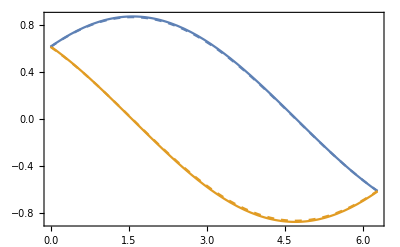

```mathematica
E1LukinK[ϕ_]:={Sqrt[0.75](Sin[ϕ/2-π/4]),Sqrt[0.75](Sin[ϕ/2+π/4])};
E2LukinK[ϕ_]:={Sqrt[0.75](Sin[ϕ/2+π/4]),-Sqrt[0.75](Sin[ϕ/2-π/4])};

GrapE1kp=Plot[{2^(1/4)Re[E1xK[0.03Norm[k0],ϕ,0,0]],2^(1/4)Re[E1yK[0.03Norm[k0],ϕ,0,0]]},{ϕ,0,2π},Frame->True,LabelStyle->Directive[Bold, Medium]];
GrapE1Lukin=Plot[{E1LukinK[ϕ]⟦1⟧,E1LukinK[ϕ]⟦2⟧},{ϕ,0,2π},PlotStyle->Dashed];
Show[GrapE1kp,GrapE1Lukin,PlotRange->All];

GrapE2kp=Plot[{2^(1/4)Re[E2xK[0.03Norm[k0],ϕ,0,0]],2^(1/4)Re[E2yK[0.03Norm[k0],ϕ,0,0]]},{ϕ,0,2π},Frame->True,LabelStyle->Directive[Bold, Medium]];
GrapE2Lukin=Plot[{E2LukinK[ϕ][[1]],E2LukinK[ϕ][[2]]},{ϕ,0,2π},PlotStyle->Dashed];
Show[GrapE2kp,GrapE2Lukin,PlotRange->All]
```

#### Field Functions around Kp

```mathematica
Clear[Δk,R,Xx,Yy]
Δk[k_,ϕ_]:=k{Cos[ϕ],Sin[ϕ]};
k0={kx,-ky};
Clear[x,y,z]
TK0i=AbsoluteTime[];
{Kp,frecsKp,CoefMMKp,HxxKp,HyyKp,HzzKp,DxxKp,DyyKp,DzzKp}=WVrec[k0,nb,1];
TK0f=AbsoluteTime[]-TK0i;
```

```mathematica
MKp=Partition[Import["M-kx_"<>ToString[k0⟦1⟧]<>"-ky_"<>ToString[k0⟦2⟧]<>"-gmax_"<>ToString[gx]<>"-Ng_"<>ToString[Ng]<>".dat","Table"],2];
mKp=Sum[Norm[MKp⟦i,j⟧],{i,2},{j,2}]/4;
```

```mathematica
D0Kp=DxxKp/.z->0 /.x->0 /.y->0;
θEKp={ArcTan[Re[D0Kp⟦1⟧],Im[D0Kp⟦1⟧]],ArcTan[Re[D0Kp⟦2⟧],Im[D0Kp⟦2⟧]]};
CoefMMKp=Chop[CoefMMKp*Exp[-ⅈ θEKp]];
{HzzKp,DxxKp,DyyKp}={Chop[HzzKp*Exp[-ⅈ θEKp]],Chop[DxxKp*Exp[-ⅈ θEKp]],Chop[DyyKp*Exp[-ⅈ θEKp]]};
Clear[HxxKp,HyyKp,DzzKp]
```

```mathematica
ϕKp=ArcTan[Kp⟦1⟧,Kp⟦2⟧];
f0Kp=Mean[frecsKp];
f1Kp[qq_]=Sqrt[(f0Kp*2π)^2+mKp qq]/(2π);
f2Kp[qq_]=Sqrt[(f0Kp*2π)^2-mKp qq]/(2π);
V1Kp[ϕ_]={Sin[(ϕ-ϕKp)/2],Cos[(ϕ-ϕKp)/2]};
V2Kp[ϕ_]={-Cos[(ϕ-ϕKp)/2],Sin[(ϕ-ϕKp)/2]};
Clear[E1x0Kp,E1y0Kp,E2x0Kp,E2y0Kp,E1xKp,E1yKp,E2xKp,E2yKp,Dx0Kp,Dy0Kp,Hz0Kp];
Dx0Kp[xp_,yp_]=(DxxKp/.y->yp/.x->xp/.z->0);
Dy0Kp[xp_,yp_]=(DyyKp/.y->yp/.x->xp/.z->0);
Hz0Kp[xp_,yp_]= HzzKp/.y->yp/.x->xp/.z->0;
```

```mathematica
E1x0Kp[k_,ϕ_,x_,y_]:=E1x0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0Kp[x,y]⟦1⟧)(2π f0Kp)/Eps[x,y];
E2x0Kp[k_,ϕ_,x_,y_]:=E2x0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0Kp[x,y]⟦2⟧)(2π f0Kp)/Eps[x,y];
E1y0Kp[k_,ϕ_,x_,y_]:=E1y0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0Kp[x,y]⟦1⟧)(2π f0Kp)/Eps[x,y];
E2y0Kp[k_,ϕ_,x_,y_]:=E2y0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0Kp[x,y]⟦2⟧)(2π f0Kp)/Eps[x,y];

D1x0Kp[k_,ϕ_,x_,y_]:=D1x0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0Kp[x,y]⟦1⟧)(2π f0Kp);
D2x0Kp[k_,ϕ_,x_,y_]:=D2x0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dx0Kp[x,y]⟦2⟧)(2π f0Kp);
D1y0Kp[k_,ϕ_,x_,y_]:=D1y0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0Kp[x,y]⟦1⟧)(2π f0Kp);
D2y0Kp[k_,ϕ_,x_,y_]:=D2y0Kp[k,ϕ,x,y]=(Exp[ⅈ Δk[k,ϕ].{x,y}]Dy0Kp[x,y]⟦2⟧)(2π f0Kp);

E1xKp[k_,ϕ_,x_,y_]:=(V1Kp[ϕ]⟦1⟧(E1x0Kp[k,ϕ,x,y])+V1Kp[ϕ]⟦2⟧(E2x0Kp[k,ϕ,x,y]))/(2π f1Kp[k]);
E1yKp[k_,ϕ_,x_,y_]:=(V1Kp[ϕ]⟦1⟧(E1y0Kp[k,ϕ,x,y])+V1Kp[ϕ]⟦2⟧(E2y0Kp[k,ϕ,x,y]))/(2π f1Kp[k]);
E2xKp[k_,ϕ_,x_,y_]:=(V2Kp[ϕ]⟦1⟧(E1x0Kp[k,ϕ,x,y])+V2Kp[ϕ]⟦2⟧(E2x0Kp[k,ϕ,x,y]))/(2π f2Kp[k]);
E2yKp[k_,ϕ_,x_,y_]:=(V2Kp[ϕ]⟦1⟧(E1y0Kp[k,ϕ,x,y])+V2Kp[ϕ]⟦2⟧(E2y0Kp[k,ϕ,x,y]))/(2π f2Kp[k]);

D1xKp[k_,ϕ_,x_,y_]:=(V1Kp[ϕ]⟦1⟧(D1x0Kp[k,ϕ,x,y])+V1Kp[ϕ]⟦2⟧(D2x0Kp[k,ϕ,x,y]))/(2π f1Kp[k]);
D1yKp[k_,ϕ_,x_,y_]:=(V1Kp[ϕ]⟦1⟧(D1y0Kp[k,ϕ,x,y])+V1Kp[ϕ]⟦2⟧(D2y0Kp[k,ϕ,x,y]))/(2π f1Kp[k]);
D2xKp[k_,ϕ_,x_,y_]:=(V2Kp[ϕ]⟦1⟧(D1x0Kp[k,ϕ,x,y])+V2Kp[ϕ]⟦2⟧(D2x0Kp[k,ϕ,x,y]))/(2π f2Kp[k]);
D2yKp[k_,ϕ_,x_,y_]:=(V2Kp[ϕ]⟦1⟧(D1y0Kp[k,ϕ,x,y])+V2Kp[ϕ]⟦2⟧(D2y0Kp[k,ϕ,x,y]))/(2π f2Kp[k]);
```

Comparison with Lukin
Here, we compare the fields of the k·p method with the ansatz proposed by Lukin at the center of the unit cell. It is made for the fields around tghe point K.
NOTE: The calculations made here use and specific form for the eigenvectors V1K and V2K that is correct for the basis of gx=9 and Ng=3, for other basis it is possible that these vector change by permutation of the sinusoidal functions or signs.

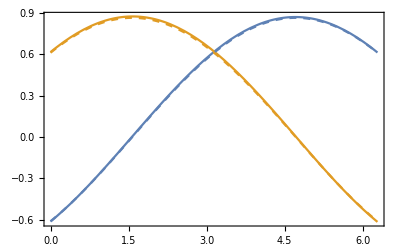

```mathematica
E1LukinKp[ϕ_]:={Sqrt[0.75](Sin[ϕ/2+π/4]),-Sqrt[0.75](Sin[ϕ/2-π/4])};
E2LukinKp[ϕ_]:={Sqrt[0.75](Sin[ϕ/2-π/4]),Sqrt[0.75](Sin[ϕ/2+π/4])};

GrapE1kp=Plot[{2^(1/4)Re[E1xKp[0.03Norm[k0],ϕ,0,0]],2^(1/4)Re[E1yKp[0.03Norm[k0],ϕ,0,0]]},{ϕ,0,2π},Frame->True,LabelStyle->Directive[Bold, Medium]];
GrapE1Lukin=Plot[{E1LukinKp[ϕ]⟦1⟧,E1LukinKp[ϕ]⟦2⟧},{ϕ,0,2π},PlotStyle->Dashed];
Show[GrapE1kp,GrapE1Lukin,PlotRange->All];

GrapE2kp=Plot[{2^(1/4)Re[E2xKp[0.03Norm[k0],ϕ,0,0]],2^(1/4)Re[E2yKp[0.03Norm[k0],ϕ,0,0]]},{ϕ,0,2π},Frame->True,LabelStyle->Directive[Bold, Medium]];
GrapE2Lukin=Plot[{E2LukinKp[ϕ]⟦1⟧,E2LukinKp[ϕ]⟦2⟧},{ϕ,0,2π},PlotStyle->Dashed];
Show[GrapE2kp,GrapE2Lukin,PlotRange->All]
```

## Green Function

Here, we define Green’s function in linear polarization.

### Green Function Using k.P

#### Coefficients from GME — K y K’

```mathematica
E1K[x_,y_]:=E1K[x,y]={Dx0K[x,y]⟦1⟧,Dy0K[x,y]⟦1⟧}/Eps[x,y];
E2K[x_,y_]:=E2K[x,y]={Dx0K[x,y]⟦2⟧,Dy0K[x,y]⟦2⟧}/Eps[x,y];
E1Kp[x_,y_]:=E1Kp[x,y]={Dx0Kp[x,y]⟦1⟧,Dy0Kp[x,y]⟦1⟧}/Eps[x,y];
E2Kp[x_,y_]:=E2Kp[x,y]={Dx0Kp[x,y]⟦2⟧,Dy0Kp[x,y]⟦2⟧}/Eps[x,y];
```

```mathematica
Clear[AK,BK,CK,AKp,BKp,CKp]
AK[x_,y_,α_,β_]:=AK[x,y,α,β]=E1K[x,y]⟦α⟧*E1K[x,y]⟦β⟧+E2K[x,y]⟦α⟧*E2K[x,y]⟦β⟧;
BK[x_,y_,α_,β_]:=BK[x,y,α,β]=E1K[x,y]⟦α⟧*E1K[x,y]⟦β⟧-E2K[x,y]⟦α⟧*E2K[x,y]⟦β⟧;
CK[x_,y_,α_,β_]:=CK[x,y,α,β]=E1K[x,y]⟦α⟧*E2K[x,y]⟦β⟧+E2K[x,y]⟦α⟧*E1K[x,y]⟦β⟧;

AKpN[x_,y_,α_,β_]:=AKpN[x,y,α,β]=E1Kp[x,y]⟦α⟧*E1Kp[x,y]⟦β⟧+E2Kp[x,y]⟦α⟧*E2Kp[x,y]⟦β⟧;
BKpN[x_,y_,α_,β_]:=BKpN[x,y,α,β]=E1Kp[x,y]⟦α⟧*E1Kp[x,y]⟦β⟧-E2Kp[x,y]⟦α⟧*E2Kp[x,y]⟦β⟧;
CKpN[x_,y_,α_,β_]:=CKpN[x,y,α,β]=E1Kp[x,y]⟦α⟧*E2Kp[x,y]⟦β⟧+E2Kp[x,y]⟦α⟧*E1Kp[x,y]⟦β⟧;
AKp[x_,y_,α_,β_]:=AKp[x,y,α,β]=AK[x,y,α,β]*;
BKp[x_,y_,α_,β_]:=BKp[x,y,α,β]=-BK[x,y,α,β]*/2+Sqrt[3]CK[x,y,α,β]*/2;
CKp[x_,y_,α_,β_]:=CKp[x,y,α,β]=Sqrt[3]BK[x,y,α,β]*/2+CK[x,y,α,β]*/2;
```

#### Green Function — K y K’

```mathematica
(*Parameters of the Green's functions*)
λ=738*10^(-9)//N;
areal=0.439*λ//N;
creal=3*10^8//N;
m=Mean[{mK,mKp}];
f0=Mean[{f0K,f0Kp}];
ωA=(2π creal/areal) f0//N;
fA=creal/areal f0//N;
vs=m/(4π f0) creal//N;
δA=2π 19.5*10^9(*en unidades SI --- approx 1-100 GHz*);
ap=areal{Sqrt[3]/2,1/2};
am=areal{-Sqrt[3]/2,1/2};
R=5ap;
```

```mathematica
G[δA_,r_,ϕϕ_,x_,y_,α_,β_]:=S  creal^2/(2π)^2((π^2δA)/(2ωA vs^2))(Exp[ⅈ (K/areal).{r Cos[ϕϕ],r Sin[ϕϕ]}](ⅈ HankelH1[0,r δA/vs]AK[x,y,α,β]-HankelH1[1,r δA/vs](BK[x,y,α,β]Cos[ϕK-ϕϕ]-CK[x,y,α,β]Sin[ϕK-ϕϕ]))
+Exp[ⅈ (Kp/areal).{r Cos[ϕϕ],r Sin[ϕϕ]}](ⅈ HankelH1[0,r δA/vs]AKp[x,y,α,β]-HankelH1[1,r δA/vs](BKp[x,y,α,β]Cos[ϕKp-ϕϕ]+CKp[x,y,α,β]Sin[ϕKp-ϕϕ])));
(*Here, the sign of accompanying the coefficients BK, CK, BKp and CKp can change depending of the basis we are considered. The sign's configuration we have here are {+,-,+,+} for the coefficients BK, CK, BKp,CKp}, respectively; this choice is concordant with a basis of gx=9 or gx=18 and Ng=3*)
```

## Graph decay for several points

Here, we evaluated the two-point Green function for different distances (R) between homologouos points in two unit cells. And using the assymptotic behaviour we fit the numercial results to a power-law. Here, we present the γ, ϵ G_αβ(r1; a1), and log[10,W1] for the different components of Green’s functions, the r1 is evaluated in the whole unit cell.

### Unite cell, evaluating mesh

5313

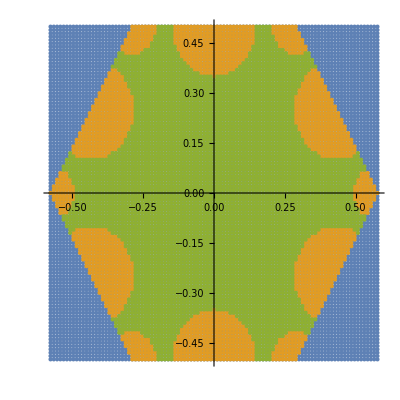
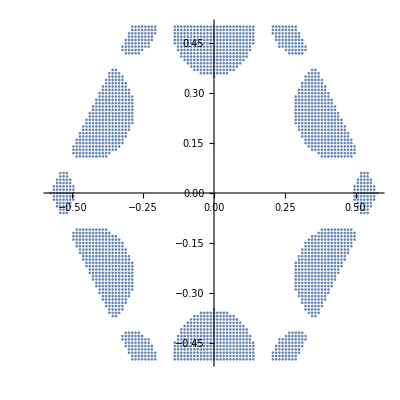

```mathematica
Nx=Ny=100;
Rlist=Flatten[Table[N[{xx,yy}],{xx,-Sqrt[3]/3,Sqrt[3]/3,2Sqrt[3]/(3*Nx)},{yy,-0.5,0.5,1/Ny}],1];
RHex={};
Rdiel={};
Do[{xX,yY}=Rlist⟦i⟧;
If[(Abs[xX]≤ Sqrt[3]/6 && Abs[yY] <=0.5),AppendTo[RHex,{xX,yY}],If[Abs[xX]≥  Sqrt[3]/6&& Abs[yY]≤  -Sqrt[3]Abs[xX]+1,AppendTo[RHex,{xX,yY}]]],{i,1,Length[Rlist]}];
Do[{xX,yY}=RHex⟦i⟧;
If[Eps[xX,yY]≠ 1.0,AppendTo[Rdiel,{xX,yY}]],{i,1,Length[RHex]}];
Print[Length[Rdiel]]
Rair=Complement[RHex,Rdiel];
{ListPlot[{Rlist,Rair,Rdiel},AspectRatio->1,PlotStyle->PointSize[Medium]],ListPlot[{Rair},AspectRatio->1]}
```

### Fit Module

```mathematica
PowerFit[x0_,y0_,α0_,β0_]:=Module[{xx=x0,yy=y0,αα=α0,ββ=β0},
θ={π/6,π/2,5π/6};
data1={};data2={};data3={};
rdata1={};rdata2={};rdata3={};
idata1={};idata2={};idata3={};
Do[G1=Table[G[δA,(i+n) Norm[ap],θ⟦1⟧,xx,yy,αα,ββ],{n,0,2}];
G2=Table[G[δA,(i+n) Norm[ap],θ⟦2⟧,xx,yy,αα,ββ],{n,0,2}];
G3=Table[G[δA,(i+n) Norm[ap],θ⟦3⟧,xx,yy,αα,ββ],{n,0,2}];

AppendTo[data1,{i-1+Position[Abs[G1],Max[Abs[G1]]]⟦1,1⟧,Max[Abs[G1]]}];
AppendTo[data2,{i-1+Position[Abs[G2],Max[Abs[G2]]]⟦1,1⟧,Max[Abs[G2]]}];
AppendTo[data3,{i-1+Position[Abs[G3],Max[Abs[G3]]]⟦1,1⟧,Max[Abs[G3]]}];
AppendTo[rdata1,{i-1+Position[Abs[Re[G1]],Max[Abs[Re[G1]]]]⟦1,1⟧,Max[Abs[Re[G1]]]}];
AppendTo[rdata2,{i-1+Position[Abs[Re[G2]],Max[Abs[Re[G2]]]]⟦1,1⟧,Max[Abs[Re[G2]]]}];
AppendTo[rdata3,{i-1+Position[Abs[Re[G3]],Max[Abs[Re[G3]]]]⟦1,1⟧,Max[Abs[Re[G3]]]}];
AppendTo[idata1,{i-1+Position[Abs[Im[G1]],Max[Abs[Im[G1]]]]⟦1,1⟧,Max[Abs[Im[G1]]]}];
AppendTo[idata2,{i-1+Position[Abs[Im[G2]],Max[Abs[Im[G2]]]]⟦1,1⟧,Max[Abs[Im[G2]]]}];
AppendTo[idata3,{i-1+Position[Abs[Im[G3]],Max[Abs[Im[G3]]]]⟦1,1⟧,Max[Abs[Im[G3]]]}];
,{i,1,91,3}];

Clear[Aa1,τa1,Aa2,τa2,Aa3,τa3,Ar1,τr1,Ar2,τr2,Ar3,τr3,Ai1,τi1,Ai2,τi2,Ai3,τi3];
f1=NonlinearModelFit[data1,Aa1 /x^τa1,{Aa1,τa1},x];
f2=NonlinearModelFit[data2,Aa2 /x^τa2,{Aa2,τa2},x];
f3=NonlinearModelFit[data3,Aa3 /x^τa3,{Aa3,τa3},x];
fr1=NonlinearModelFit[rdata1,Ar1/ x^τr1,{Ar1,τr1},x];
fr2=NonlinearModelFit[rdata2,Ar2/ x^τr2,{Ar2,τr2},x];
fr3=NonlinearModelFit[rdata3,Ar3 /x^τr3,{Ar3,τr3},x];
fi1=NonlinearModelFit[idata1,Ai1 /x^τi1,{Ai1,τi1},x];
fi2=NonlinearModelFit[idata2,Ai2 /x^τi2,{Ai2,τi2},x];
fi3=NonlinearModelFit[idata3,Ai3 /x^τi3,{Ai3,τi3},x];

Do[(*Fit verification for π/6*)
If[(Abs[G[δA,i Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]-f1[i])/f1[i]>0.09,data1⟦1⟧={i,Abs[G[δA,i areal,θ⟦1⟧,xx,yy,αα,ββ]]};f1=NonlinearModelFit[data1,Aa1 /x^τt1,{Aa1,τt1},x]];
If[(Abs[Re[G[δA,i Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]]-fr1[i])/fr1[i]>0.09,rdata1⟦1⟧={i,Abs[Re[G[δA,i areal,θ⟦1⟧,xx,yy,αα,ββ]]]};fr1=NonlinearModelFit[rdata1,Aar1/ x^τtr1,{Aar1,τtr1},x]];
If[(Abs[Im[G[δA,i Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]]-fi1[i])/fi1[i]>0.09,idata1⟦1⟧={i,Abs[Im[G[δA,i areal,θ⟦1⟧,xx,yy,αα,ββ]]]};fi1=NonlinearModelFit[idata1,Aai1 /x^τti1,{Aai1,τti1},x]];
(*Fit verification for π/2*)
If[(Abs[G[δA,i Norm[ap],θ⟦2⟧,xx,yy,αα,ββ]]-f2[i])/f2[i]>0.09,data2⟦1⟧={i,Abs[G[δA,i areal,θ⟦2⟧,xx,yy,αα,ββ]]};f2=NonlinearModelFit[data2,Aa2 /x^τt2,{Aa2,τt2},x]];
If[(Abs[Re[G[δA,i Norm[ap],θ⟦2⟧,xx,yy,αα,ββ]]]-fr2[i])/fr2[i]>0.09,rdata2⟦1⟧={i,Abs[Re[G[δA,i areal,θ⟦2⟧,xx,yy,αα,ββ]]]};fr2=NonlinearModelFit[rdata2,Aar2/ x^τtr2,{Aar2,τtr2},x]];
If[(Abs[Im[G[δA,i Norm[ap],θ⟦2⟧,xx,yy,αα,ββ]]]-fi2[i])/fi2[i]>0.09,idata2⟦1⟧={i,Abs[Im[G[δA,i areal,θ⟦2⟧,xx,yy,αα,ββ]]]};fi2=NonlinearModelFit[idata2,Aai2 /x^τti2,{Aai2,τti2},x]];
(*Fit verification for 5π/6*)
If[(Abs[G[δA,i Norm[ap],θ⟦3⟧,xx,yy,αα,ββ]]-f3[i])/f3[i]>0.09,data3⟦1⟧={i,Abs[G[δA,i areal,θ⟦3⟧,xx,yy,αα,ββ]]};f3=NonlinearModelFit[data3,Aa3 /x^τt3,{Aa3,τt3},x]];
If[(Abs[Re[G[δA,i Norm[ap],θ⟦3⟧,xx,yy,αα,ββ]]]-fr3[i])/fr3[i]>0.09,rdata3⟦1⟧={i,Abs[Re[G[δA,i areal,θ⟦3⟧,xx,yy,αα,ββ]]]};fr3=NonlinearModelFit[rdata3,Aar3/ x^τtr3,{Aar3,τtr3},x]];
If[(Abs[Im[G[δA,i Norm[ap],θ⟦3⟧,xx,yy,αα,ββ]]]-fi3[i])/fi3[i]>0.09,idata3⟦1⟧={i,Abs[Im[G[δA,i areal,θ⟦3⟧,xx,yy,αα,ββ]]]};fi3=NonlinearModelFit[idata3,Aai3 /x^τti3,{Aai3,τti3},x]];
,{i,2,3}];

{Aa1,τa1}=f1["BestFitParameters"]⟦All,2⟧;rsq1=f1["RSquared"];
{Aa2,τa2}=f2["BestFitParameters"]⟦All,2⟧;rsq2=f2["RSquared"];
{Aa3,τa3}=f3["BestFitParameters"]⟦All,2⟧;rsq3=f3["RSquared"];

{Ar1,τr1}=fr1["BestFitParameters"]⟦All,2⟧;rsqr1=fr1["RSquared"];
{Ar2,τr2}=fr2["BestFitParameters"]⟦All,2⟧;rsqr2=fr2["RSquared"];
{Ar3,τr3}=fr3["BestFitParameters"]⟦All,2⟧;rsqr3=fr3["RSquared"];

{Ai1,τi1}=fi1["BestFitParameters"]⟦All,2⟧;rsqi1=fi1["RSquared"];
{Ai2,τi2}=fi2["BestFitParameters"]⟦All,2⟧;rsqi2=fi2["RSquared"];
{Ai3,τi3}=fi3["BestFitParameters"]⟦All,2⟧;rsqi3=fi3["RSquared"];
{{{Aa1,τa1,rsq1},{Ar1,τr1,rsqr1},{Ai1,τi1,rsqi1}},{{Aa2,τa2,rsq2},{Ar2,τr2,rsqr2},{Ai2,τi2,rsqi2}},{{Aa3,τa3,rsq3},{Ar3,τr3,rsqr3},{Ai3,τi3,rsqi3}}} (*dimensions {3,3,3}...⟦Chose angle; chose Abs-real-im; chose A-γ-R^2⟧*)
]
```

```mathematica
PowerFitN[x0_,y0_,α0_,β0_]:=Module[{xx=x0,yy=y0,αα=α0,ββ=β0},
θ={π/6,π/2,5π/6};
δN=10;
data1={};data2={};data3={};
rdata1={};rdata2={};rdata3={};
idata1={};idata2={};idata3={};
Do[G1=Table[G[δA,(i+n) Norm[ap],θ⟦1⟧,xx,yy,αα,ββ],{n,0,2}];
G2=Table[G[δA,(i+n) Norm[ap],θ⟦2⟧,xx,yy,αα,ββ],{n,0,2}];
G3=Table[G[δA,(i+n) Norm[ap],θ⟦3⟧,xx,yy,αα,ββ],{n,0,2}];

AppendTo[data1,{i-1+Position[Abs[G1],Max[Abs[G1]]]⟦1,1⟧,Max[Abs[G1]]}];
AppendTo[data2,{i-1+Position[Abs[G2],Max[Abs[G2]]]⟦1,1⟧,Max[Abs[G2]]}];
AppendTo[data3,{i-1+Position[Abs[G3],Max[Abs[G3]]]⟦1,1⟧,Max[Abs[G3]]}];
AppendTo[rdata1,{i-1+Position[Abs[Re[G1]],Max[Abs[Re[G1]]]]⟦1,1⟧,Max[Abs[Re[G1]]]}];
AppendTo[rdata2,{i-1+Position[Abs[Re[G2]],Max[Abs[Re[G2]]]]⟦1,1⟧,Max[Abs[Re[G2]]]}];
AppendTo[rdata3,{i-1+Position[Abs[Re[G3]],Max[Abs[Re[G3]]]]⟦1,1⟧,Max[Abs[Re[G3]]]}];
AppendTo[idata1,{i-1+Position[Abs[Im[G1]],Max[Abs[Im[G1]]]]⟦1,1⟧,Max[Abs[Im[G1]]]}];
AppendTo[idata2,{i-1+Position[Abs[Im[G2]],Max[Abs[Im[G2]]]]⟦1,1⟧,Max[Abs[Im[G2]]]}];
AppendTo[idata3,{i-1+Position[Abs[Im[G3]],Max[Abs[Im[G3]]]]⟦1,1⟧,Max[Abs[Im[G3]]]}];
,{i,δN,91,3}];

Clear[Aa1,τa1,Aa2,τa2,Aa3,τa3,Ar1,τr1,Ar2,τr2,Ar3,τr3,Ai1,τi1,Ai2,τi2,Ai3,τi3];
f1=NonlinearModelFit[data1,Aa1/ x^τa1,{Aa1,τa1},x];
f2=NonlinearModelFit[data2,Aa2 /x^τa2,{Aa2,τa2},x];
f3=NonlinearModelFit[data3,Aa3 /x^τa3,{Aa3,τa3},x];
fr1=NonlinearModelFit[rdata1,Ar1/ x^τr1,{Ar1,τr1},x];
fr2=NonlinearModelFit[rdata2,Ar2 /x^τr2,{Ar2,τr2},x];
fr3=NonlinearModelFit[rdata3,Ar3 /x^τr3,{Ar3,τr3},x];
fi1=NonlinearModelFit[idata1,Ai1 /x^τi1,{Ai1,τi1},x];
fi2=NonlinearModelFit[idata2,Ai2 /x^τi2,{Ai2,τi2},x];
fi3=NonlinearModelFit[idata3,Ai3 /x^τi3,{Ai3,τi3},x];

{Aa1,τa1}=f1["BestFitParameters"]⟦All,2⟧;rsq1=f1["RSquared"];
{Aa2,τa2}=f2["BestFitParameters"]⟦All,2⟧;rsq2=f2["RSquared"];
{Aa3,τa3}=f3["BestFitParameters"]⟦All,2⟧;rsq3=f3["RSquared"];

{Ar1,τr1}=fr1["BestFitParameters"]⟦All,2⟧;rsqr1=fr1["RSquared"];
{Ar2,τr2}=fr2["BestFitParameters"]⟦All,2⟧;rsqr2=fr2["RSquared"];
{Ar3,τr3}=fr3["BestFitParameters"]⟦All,2⟧;rsqr3=fr3["RSquared"];

{Ai1,τi1}=fi1["BestFitParameters"]⟦All,2⟧;rsqi1=fi1["RSquared"];
{Ai2,τi2}=fi2["BestFitParameters"]⟦All,2⟧;rsqi2=fi2["RSquared"];
{Ai3,τi3}=fi3["BestFitParameters"]⟦All,2⟧;rsqi3=fi3["RSquared"];
{{{Aa1,τa1,rsq1},{Ar1,τr1,rsqr1},{Ai1,τi1,rsqi1}},{{Aa2,τa2,rsq2},{Ar2,τr2,rsqr2},{Ai2,τi2,rsqi2}},{{Aa3,τa3,rsq3},{Ar3,τr3,rsqr3},{Ai3,τi3,rsqi3}}} (*dimensions {3,3,3}...⟦Chose angle; chose Abs-real-im; chose A-γ-R^2⟧*)
]
```

### Gxx

#### Fit Model

```mathematica
αα=1;ββ=1;θ={π/6,π/2,5π/6};
γ1d1={};γ1d2={};γ1d3={};γ1a1={};γ1a2={};γ1a3={};
A1d1={};A1d2={};A1d3={};A1a1={};A1a2={};A1a3={};
Rsq1d1={};Rsq1d2={};Rsq1d3={};Rsq1a1={};Rsq1a2={};Rsq1a3={};

γ1dr1={};γ1dr2={};γ1dr3={};γ1ar1={};γ1ar2={};γ1ar3={};
A1dr1={};A1dr2={};A1dr3={};A1ar1={};A1ar2={};A1ar3={};
Rsq1dr1={};Rsq1dr2={};Rsq1dr3={};Rsq1ar1={};Rsq1ar2={};Rsq1ar3={};

γ1di1={};γ1di2={};γ1di3={};γ1ai1={};γ1ai2={};γ1ai3={};
A1di1={};A1di2={};A1di3={};A1ai1={};A1ai2={};A1ai3={};
Rsq1di1={};Rsq1di2={};Rsq1di3={};Rsq1ai1={};Rsq1ai2={};Rsq1ai3={};
```

```mathematica
TdieGxx0=AbsoluteTime[]; 
Do[tγ0=AbsoluteTime[];
{xx,yy}=Rdiel⟦j⟧;
{Fit1,Fit2,Fit3}=PowerFit[xx,yy,αα,ββ];

AppendTo[γ1d1,{xx,yy,Fit1⟦1,2⟧}];AppendTo[A1d1,{xx,yy,Fit1⟦1,1⟧}];AppendTo[Rsq1d1,{xx,yy,Fit1⟦1,3⟧}];
AppendTo[γ1d2,{xx,yy,Fit2⟦1,2⟧}];AppendTo[A1d2,{xx,yy,Fit2⟦1,1⟧}];AppendTo[Rsq1d2,{xx,yy,Fit2⟦1,3⟧}];
AppendTo[γ1d3,{xx,yy,Fit3⟦1,2⟧}];AppendTo[A1d3,{xx,yy,Fit3⟦1,1⟧}];AppendTo[Rsq1d3,{xx,yy,Fit3⟦1,3⟧}];

AppendTo[γ1dr1,{xx,yy,Fit1⟦2,2⟧}];AppendTo[A1dr1,{xx,yy,Fit1⟦2,1⟧}];AppendTo[Rsq1dr1,{xx,yy,Fit1⟦2,3⟧}];
AppendTo[γ1dr2,{xx,yy,Fit2⟦2,2⟧}];AppendTo[A1dr2,{xx,yy,Fit2⟦2,1⟧}];AppendTo[Rsq1dr2,{xx,yy,Fit2⟦2,3⟧}];
AppendTo[γ1dr3,{xx,yy,Fit3⟦2,2⟧}];AppendTo[A1dr3,{xx,yy,Fit3⟦2,1⟧}];AppendTo[Rsq1dr3,{xx,yy,Fit3⟦2,3⟧}];

AppendTo[γ1di1,{xx,yy,Fit1⟦3,2⟧}];AppendTo[A1di1,{xx,yy,Fit1⟦3,1⟧}];AppendTo[Rsq1di1,{xx,yy,Fit1⟦3,3⟧}];
AppendTo[γ1di2,{xx,yy,Fit2⟦3,2⟧}];AppendTo[A1di2,{xx,yy,Fit2⟦3,1⟧}];AppendTo[Rsq1di2,{xx,yy,Fit2⟦3,3⟧}];
AppendTo[γ1di3,{xx,yy,Fit3⟦3,2⟧}];AppendTo[A1di3,{xx,yy,Fit3⟦3,1⟧}];AppendTo[Rsq1di3,{xx,yy,Fit3⟦3,3⟧}];
,{j,Length[Rdiel]}]
TdieGxx=AbsoluteTime[]-TdieGxx0
TairGxx0=AbsoluteTime[]; 
Do[tγ0=AbsoluteTime[];
{xx,yy}=Rair⟦j⟧;
{Fit1,Fit2,Fit3}=PowerFit[xx,yy,αα,ββ];

AppendTo[γ1a1,{xx,yy,Fit1⟦1,2⟧}];AppendTo[A1a1,{xx,yy,Fit1⟦1,1⟧}];AppendTo[Rsq1a1,{xx,yy,Fit1⟦1,3⟧}];
AppendTo[γ1a2,{xx,yy,Fit2⟦1,2⟧}];AppendTo[A1a2,{xx,yy,Fit2⟦1,1⟧}];AppendTo[Rsq1a2,{xx,yy,Fit2⟦1,3⟧}];
AppendTo[γ1a3,{xx,yy,Fit3⟦1,2⟧}];AppendTo[A1a3,{xx,yy,Fit3⟦1,1⟧}];AppendTo[Rsq1a3,{xx,yy,Fit3⟦1,3⟧}];

AppendTo[γ1ar1,{xx,yy,Fit1⟦2,2⟧}];AppendTo[A1ar1,{xx,yy,Fit1⟦2,1⟧}];AppendTo[Rsq1ar1,{xx,yy,Fit1⟦2,3⟧}];
AppendTo[γ1ar2,{xx,yy,Fit2⟦2,2⟧}];AppendTo[A1ar2,{xx,yy,Fit2⟦2,1⟧}];AppendTo[Rsq1ar2,{xx,yy,Fit2⟦2,3⟧}];
AppendTo[γ1ar3,{xx,yy,Fit3⟦2,2⟧}];AppendTo[A1ar3,{xx,yy,Fit3⟦2,1⟧}];AppendTo[Rsq1ar3,{xx,yy,Fit3⟦2,3⟧}];

AppendTo[γ1ai1,{xx,yy,Fit1⟦3,2⟧}];AppendTo[A1ai1,{xx,yy,Fit1⟦3,1⟧}];AppendTo[Rsq1ai1,{xx,yy,Fit1⟦3,3⟧}];
AppendTo[γ1ai2,{xx,yy,Fit2⟦3,2⟧}];AppendTo[A1ai2,{xx,yy,Fit2⟦3,1⟧}];AppendTo[Rsq1ai2,{xx,yy,Fit2⟦3,3⟧}];
AppendTo[γ1ai3,{xx,yy,Fit3⟦3,2⟧}];AppendTo[A1ai3,{xx,yy,Fit3⟦3,1⟧}];AppendTo[Rsq1ai3,{xx,yy,Fit3⟦3,3⟧}];
,{j,Length[Rair]}]
TairGxx=AbsoluteTime[]-TairGxx0
```

355.3866469

151.475199

```mathematica
GraphicsGrid[{{ListDensityPlot[Rsq1d1,PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic],
ListDensityPlot[Rsq1dr1,PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic],
ListDensityPlot[Rsq1di1,PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic]}},ImageSize->Full]
```

-Graphics-

#### Graphics for π/6

```mathematica
LogA1dri1=Table[{A1d1⟦i,1⟧,A1d1⟦i,2⟧,Log[10,A1dr1⟦i,3⟧/A1di1⟦i,3⟧]},{i,Length[A1d1]}];
LogA1ari1=Table[{A1a1⟦i,1⟧,A1a1⟦i,2⟧,Log[10,A1ar1⟦i,3⟧/A1ai1⟦i,3⟧]},{i,Length[A1a1]}];
LogA11=Join[LogA1dri1,LogA1ari1];
A1d1Norm=Table[{A1d1⟦i,1⟧,A1d1⟦i,2⟧,A1d1⟦i,3⟧*es},{i,Length[A1d1]}];
A1a1Norm=Table[{A1a1⟦i,1⟧,A1a1⟦i,2⟧,A1a1⟦i,3⟧*er},{i,Length[A1a1]}];
LogA1d1Norm=Table[{A1d1⟦i,1⟧,A1d1⟦i,2⟧,Log10[A1d1⟦i,3⟧]},{i,Length[A1d1]}];
LogA1a1Norm=Table[{A1a1⟦i,1⟧,A1a1⟦i,2⟧,Log10[A1a1⟦i,3⟧]},{i,Length[A1a1]}];
A11Norm=Join[A1d1Norm,A1a1Norm];A11Norm⟦All,3⟧=A11Norm⟦All,3⟧/Max[A11Norm⟦All,3⟧];
LogA11Norm=Join[LogA1d1Norm,LogA1a1Norm];
A11=Join[A1d1,A1a1];
γ11=Join[γ1d1,γ1a1];

cfγ=Blend[{(*{Max[γ11⟦All,3⟧],Darker[White]},*){1,White},{0.85,LightRed},{0.4,Red},{Max[0,Min[γ11⟦All,3⟧]],Darker[Red]}},#]&;
cfA=Blend[{{0,White},{0.1(*Mean[A11Norm⟦All,3⟧]*),Yellow},{0.4,Red},{1,Darker[Red]}},#]&;
cfLogA=Blend[{(*{Min[LogA11Norm⟦All,3⟧],Darker[Blue]},*){-3,Blue},{0,White},{Max[LogA11Norm⟦All,3⟧],Red}},#]&;
cfAri=Blend[{{(*Min[LogA11⟦All,3⟧]*)-1,Blue},{0,White},{0.5Max[LogA11⟦All,3⟧],LightRed},{Max[LogA11⟦All,3⟧],Red}},#]&;
```

```mathematica
γGraph=ListDensityPlot[γ11,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfγ,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameStyle->Black];
AGraph=ListDensityPlot[A11Norm,PlotRange->{0,2},PlotLegends->BarLegend[{cfA,{0,0.4}}],ColorFunction->cfA,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameStyle->Black];
LAGraph=ListDensityPlot[LogA11Norm,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfLogA,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameStyle->Black];

LogAGraph=ListDensityPlot[LogA11,PlotRange->{0,3.1},PlotLegends->Automatic,ColorFunction->cfAri,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameStyle->Black];
```

-Graphics-

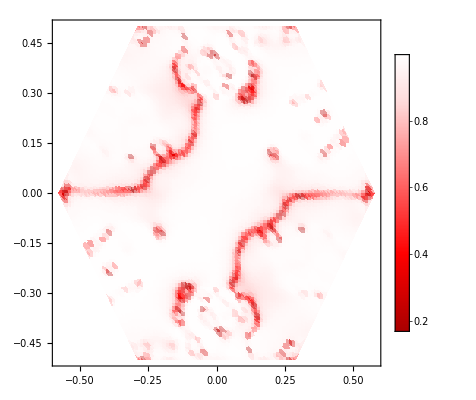

```mathematica
GraphicsGrid[{{γGraph,AGraph,LogAGraph}},ImageSize->{950,250}]
γGraph
GraphicsGrid[{{γGraph,LAGraph,LogAGraph}},ImageSize->{950,250}];
(*Export["GammaGxx-030.pdf",γGraph];Export["AmpGxx-030.pdf",AGraph]; Export["RatioReImGxx-030.pdf",LogAGraph]; *)
```

```mathematica
ArGraph=Show[{ListDensityPlot[Join[A1dr1,A1ar1],PlotRange->All,PlotLegends->Automatic,ColorFunction->"TemperatureMap",LabelStyle->Directive[Bold, Medium]]}];
AiGraph=Show[{ListDensityPlot[Join[A1di1,A1ai1],PlotRange->All,PlotLegends->Automatic,ColorFunction->"TemperatureMap",LabelStyle->Directive[Bold, Medium]]}];
GraphicsGrid[{{ArGraph,AiGraph}},ImageSize->{500,250}]
```

-Graphics-

### Gyy

#### Fit Model

```mathematica
αα=2;ββ=2;θ={π/6,π/2,5π/6};
γ2d1={};γ2d2={};γ2d3={};γ2a1={};γ2a2={};γ2a3={};
A2d1={};A2d2={};A2d3={};A2a1={};A2a2={};A2a3={};
Rsq2d1={};Rsq2d2={};Rsq2d3={};Rsq2a1={};Rsq2a2={};Rsq2a3={};

γ2dr1={};γ2dr2={};γ2dr3={};γ2ar1={};γ2ar2={};γ2ar3={};
A2dr1={};A2dr2={};A2dr3={};A2ar1={};A2ar2={};A2ar3={};
Rsq2dr1={};Rsq2dr2={};Rsq2dr3={};Rsq2ar1={};Rsq2ar2={};Rsq2ar3={};

γ2di1={};γ2di2={};γ2di3={};γ2ai1={};γ2ai2={};γ2ai3={};
A2di1={};A2di2={};A2di3={};A2ai1={};A2ai2={};A2ai3={};
Rsq2di1={};Rsq2di2={};Rsq2di3={};Rsq2ai1={};Rsq2ai2={};Rsq2ai3={};
```

```mathematica
TdieGyy0=AbsoluteTime[]; 
Do[tγ0=AbsoluteTime[];
{xx,yy}=Rdiel⟦j⟧;
{Fit1,Fit2,Fit3}=PowerFit[xx,yy,αα,ββ];

AppendTo[γ2d1,{xx,yy,Fit1⟦1,2⟧}];AppendTo[A2d1,{xx,yy,Fit1⟦1,1⟧}];AppendTo[Rsq2d1,{xx,yy,Fit1⟦1,3⟧}];
AppendTo[γ2d2,{xx,yy,Fit2⟦1,2⟧}];AppendTo[A2d2,{xx,yy,Fit2⟦1,1⟧}];AppendTo[Rsq2d2,{xx,yy,Fit2⟦1,3⟧}];
AppendTo[γ2d3,{xx,yy,Fit3⟦1,2⟧}];AppendTo[A2d3,{xx,yy,Fit3⟦1,1⟧}];AppendTo[Rsq2d3,{xx,yy,Fit3⟦1,3⟧}];

AppendTo[γ2dr1,{xx,yy,Fit1⟦2,2⟧}];AppendTo[A2dr1,{xx,yy,Fit1⟦2,1⟧}];AppendTo[Rsq2dr1,{xx,yy,Fit1⟦2,3⟧}];
AppendTo[γ2dr2,{xx,yy,Fit2⟦2,2⟧}];AppendTo[A2dr2,{xx,yy,Fit2⟦2,1⟧}];AppendTo[Rsq2dr2,{xx,yy,Fit2⟦2,3⟧}];
AppendTo[γ2dr3,{xx,yy,Fit3⟦2,2⟧}];AppendTo[A2dr3,{xx,yy,Fit3⟦2,1⟧}];AppendTo[Rsq2dr3,{xx,yy,Fit3⟦2,3⟧}];

AppendTo[γ2di1,{xx,yy,Fit1⟦3,2⟧}];AppendTo[A2di1,{xx,yy,Fit1⟦3,1⟧}];AppendTo[Rsq2di1,{xx,yy,Fit1⟦3,3⟧}];
AppendTo[γ2di2,{xx,yy,Fit2⟦3,2⟧}];AppendTo[A2di2,{xx,yy,Fit2⟦3,1⟧}];AppendTo[Rsq2di2,{xx,yy,Fit2⟦3,3⟧}];
AppendTo[γ2di3,{xx,yy,Fit3⟦3,2⟧}];AppendTo[A2di3,{xx,yy,Fit3⟦3,1⟧}];AppendTo[Rsq2di3,{xx,yy,Fit3⟦3,3⟧}];
,{j,Length[Rdiel]}]
TdieGyy=AbsoluteTime[]-TdieGyy0
TairGyy0=AbsoluteTime[]; 
Do[tγ0=AbsoluteTime[];
{xx,yy}=Rair⟦j⟧;
{Fit1,Fit2,Fit3}=PowerFit[xx,yy,αα,ββ];

AppendTo[γ2a1,{xx,yy,Fit1⟦1,2⟧}];AppendTo[A2a1,{xx,yy,Fit1⟦1,1⟧}];AppendTo[Rsq2a1,{xx,yy,Fit1⟦1,3⟧}];
AppendTo[γ2a2,{xx,yy,Fit2⟦1,2⟧}];AppendTo[A2a2,{xx,yy,Fit2⟦1,1⟧}];AppendTo[Rsq2a2,{xx,yy,Fit2⟦1,3⟧}];
AppendTo[γ2a3,{xx,yy,Fit3⟦1,2⟧}];AppendTo[A2a3,{xx,yy,Fit3⟦1,1⟧}];AppendTo[Rsq2a3,{xx,yy,Fit3⟦1,3⟧}];

AppendTo[γ2ar1,{xx,yy,Fit1⟦2,2⟧}];AppendTo[A2ar1,{xx,yy,Fit1⟦2,1⟧}];AppendTo[Rsq2ar1,{xx,yy,Fit1⟦2,3⟧}];
AppendTo[γ2ar2,{xx,yy,Fit2⟦2,2⟧}];AppendTo[A2ar2,{xx,yy,Fit2⟦2,1⟧}];AppendTo[Rsq2ar2,{xx,yy,Fit2⟦2,3⟧}];
AppendTo[γ2ar3,{xx,yy,Fit3⟦2,2⟧}];AppendTo[A2ar3,{xx,yy,Fit3⟦2,1⟧}];AppendTo[Rsq2ar3,{xx,yy,Fit3⟦2,3⟧}];

AppendTo[γ2ai1,{xx,yy,Fit1⟦3,2⟧}];AppendTo[A2ai1,{xx,yy,Fit1⟦3,1⟧}];AppendTo[Rsq2ai1,{xx,yy,Fit1⟦3,3⟧}];
AppendTo[γ2ai2,{xx,yy,Fit2⟦3,2⟧}];AppendTo[A2ai2,{xx,yy,Fit2⟦3,1⟧}];AppendTo[Rsq2ai2,{xx,yy,Fit2⟦3,3⟧}];
AppendTo[γ2ai3,{xx,yy,Fit3⟦3,2⟧}];AppendTo[A2ai3,{xx,yy,Fit3⟦3,1⟧}];AppendTo[Rsq2ai3,{xx,yy,Fit3⟦3,3⟧}];
,{j,Length[Rair]}]
TairGyy=AbsoluteTime[]-TairGyy0
```

334.871269

142.337898

```mathematica
GraphicsGrid[{{ListDensityPlot[Rsq2d1,PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic],
ListDensityPlot[Rsq2dr1,PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic],
ListDensityPlot[Rsq2di1,PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic]}},ImageSize->Full]
```

-Graphics-

#### Graphics for π/6

```mathematica
LogA2dri1=Table[{A2d1⟦i,1⟧,A2d1⟦i,2⟧,Log[10,A2dr1⟦i,3⟧/A2di1⟦i,3⟧]},{i,Length[A2d1]}];
LogA2ari1=Table[{A2a1⟦i,1⟧,A2a1⟦i,2⟧,Log[10,A2ar1⟦i,3⟧/A2ai1⟦i,3⟧]},{i,Length[A2a1]}];
LogA21=Join[LogA2dri1,LogA2ari1];
A2d1Norm=Table[{A2d1⟦i,1⟧,A2d1⟦i,2⟧,A2d1⟦i,3⟧es},{i,Length[A2d1]}];
A2a1Norm=Table[{A2a1⟦i,1⟧,A2a1⟦i,2⟧,A2a1⟦i,3⟧er},{i,Length[A2a1]}];
LogA2d1Norm=Table[{A2d1⟦i,1⟧,A2d1⟦i,2⟧,Log10[A2d1⟦i,3⟧]},{i,Length[A2d1]}];
LogA2a1Norm=Table[{A2a1⟦i,1⟧,A2a1⟦i,2⟧,Log10[A2a1⟦i,3⟧]},{i,Length[A2a1]}];
A21Norm=Join[A2d1Norm,A2a1Norm];A21Norm⟦All,3⟧=A21Norm⟦All,3⟧/Max[A21Norm⟦All,3⟧];
LogA21Norm=Join[LogA2d1Norm,LogA2a1Norm];
A21=Join[A2d1,A2a1];
γ21=Join[γ2d1,γ2a1];

cfγ=Blend[{{1,White},{0.85,LightRed},{0.4,Red},{Max[0,Min[γ21⟦All,3⟧]],Darker[Red]}},#]&;
cfA=Blend[{{0,White},{0.1(*Mean[A11Norm⟦All,3⟧]*),Yellow},{0.4,Red},{1,Darker[Red]}},#]&;
cfLogA=Blend[{{Min[LogA21Norm⟦All,3⟧],Darker[Blue]},{-3,Blue},{0,White},{Max[LogA21Norm⟦All,3⟧],Red}},#]&;
cfAri=Blend[{(*{Min[LogA21⟦All,3⟧],Blue},*){0,White},{0.5Max[LogA21⟦All,3⟧],LightRed},{Max[LogA21⟦All,3⟧],Red}},#]&;
```

```mathematica
γGraph=ListDensityPlot[γ21,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfγ,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameStyle->Black];
AGraph=ListDensityPlot[A21Norm,PlotRange->{0,2},PlotLegends->BarLegend[{cfA,{0,0.4}}],ColorFunction->cfA,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameStyle->Black];
LAGraph=ListDensityPlot[LogA21Norm,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfLogA,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameStyle->Black];

LogAGraph=ListDensityPlot[LogA21,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfAri,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameStyle->Black];
```

```mathematica
GraphicsGrid[{{γGraph,AGraph,LogAGraph}},ImageSize->{950,250}]
GraphicsGrid[{{γGraph,LAGraph,LogAGraph}},ImageSize->{950,250}];
Export["GammaGyy-030.pdf",γGraph];
Export["AmpGyy-030.pdf",AGraph]; 
Export["RatioReImGyy-030.pdf",LogAGraph];
```

-Graphics-

### Gxy

#### Fit Model

```mathematica
αα=1;ββ=2;θ={π/6,π/2,5π/6};
γ3d1={};γ3d2={};γ3d3={};γ3a1={};γ3a2={};γ3a3={};
A3d1={};A3d2={};A3d3={};A3a1={};A3a2={};A3a3={};
Rsq3d1={};Rsq3d2={};Rsq3d3={};Rsq3a1={};Rsq3a2={};Rsq3a3={};

γ3dr1={};γ3dr2={};γ3dr3={};γ3ar1={};γ3ar2={};γ3ar3={};
A3dr1={};A3dr2={};A3dr3={};A3ar1={};A3ar2={};A3ar3={};
Rsq3dr1={};Rsq3dr2={};Rsq3dr3={};Rsq3ar1={};Rsq3ar2={};Rsq3ar3={};

γ3di1={};γ3di2={};γ3di3={};γ3ai1={};γ3ai2={};γ3ai3={};
A3di1={};A3di2={};A3di3={};A3ai1={};A3ai2={};A3ai3={};
Rsq3di1={};Rsq3di2={};Rsq3di3={};Rsq3ai1={};Rsq3ai2={};Rsq3ai3={};
```

```mathematica
TdieGyy0=AbsoluteTime[]; 
Do[tγ0=AbsoluteTime[];
{xx,yy}=Rdiel⟦j⟧;
{Fit1,Fit2,Fit3}=PowerFit[xx,yy,αα,ββ];

AppendTo[γ3d1,{xx,yy,Fit1⟦1,2⟧}];AppendTo[A3d1,{xx,yy,Fit1⟦1,1⟧}];AppendTo[Rsq3d1,{xx,yy,Fit1⟦1,3⟧}];
AppendTo[γ3d2,{xx,yy,Fit2⟦1,2⟧}];AppendTo[A3d2,{xx,yy,Fit2⟦1,1⟧}];AppendTo[Rsq3d2,{xx,yy,Fit2⟦1,3⟧}];
AppendTo[γ3d3,{xx,yy,Fit3⟦1,2⟧}];AppendTo[A3d3,{xx,yy,Fit3⟦1,1⟧}];AppendTo[Rsq3d3,{xx,yy,Fit3⟦1,3⟧}];

AppendTo[γ3dr1,{xx,yy,Fit1⟦2,2⟧}];AppendTo[A3dr1,{xx,yy,Fit1⟦2,1⟧}];AppendTo[Rsq3dr1,{xx,yy,Fit1⟦2,3⟧}];
AppendTo[γ3dr2,{xx,yy,Fit2⟦2,2⟧}];AppendTo[A3dr2,{xx,yy,Fit2⟦2,1⟧}];AppendTo[Rsq3dr2,{xx,yy,Fit2⟦2,3⟧}];
AppendTo[γ3dr3,{xx,yy,Fit3⟦2,2⟧}];AppendTo[A3dr3,{xx,yy,Fit3⟦2,1⟧}];AppendTo[Rsq3dr3,{xx,yy,Fit3⟦2,3⟧}];

AppendTo[γ3di1,{xx,yy,Fit1⟦3,2⟧}];AppendTo[A3di1,{xx,yy,Fit1⟦3,1⟧}];AppendTo[Rsq3di1,{xx,yy,Fit1⟦3,3⟧}];
AppendTo[γ3di2,{xx,yy,Fit2⟦3,2⟧}];AppendTo[A3di2,{xx,yy,Fit2⟦3,1⟧}];AppendTo[Rsq3di2,{xx,yy,Fit2⟦3,3⟧}];
AppendTo[γ3di3,{xx,yy,Fit3⟦3,2⟧}];AppendTo[A3di3,{xx,yy,Fit3⟦3,1⟧}];AppendTo[Rsq3di3,{xx,yy,Fit3⟦3,3⟧}];
,{j,Length[Rdiel]}]
TdieGyy=AbsoluteTime[]-TdieGyy0
TairGyy0=AbsoluteTime[]; 
Do[tγ0=AbsoluteTime[];
{xx,yy}=Rair⟦j⟧;
{Fit1,Fit2,Fit3}=PowerFit[xx,yy,αα,ββ];

AppendTo[γ3a1,{xx,yy,Fit1⟦1,2⟧}];AppendTo[A3a1,{xx,yy,Fit1⟦1,1⟧}];AppendTo[Rsq3a1,{xx,yy,Fit1⟦1,3⟧}];
AppendTo[γ3a2,{xx,yy,Fit2⟦1,2⟧}];AppendTo[A3a2,{xx,yy,Fit2⟦1,1⟧}];AppendTo[Rsq3a2,{xx,yy,Fit2⟦1,3⟧}];
AppendTo[γ3a3,{xx,yy,Fit3⟦1,2⟧}];AppendTo[A3a3,{xx,yy,Fit3⟦1,1⟧}];AppendTo[Rsq3a3,{xx,yy,Fit3⟦1,3⟧}];

AppendTo[γ3ar1,{xx,yy,Fit1⟦2,2⟧}];AppendTo[A3ar1,{xx,yy,Fit1⟦2,1⟧}];AppendTo[Rsq3ar1,{xx,yy,Fit1⟦2,3⟧}];
AppendTo[γ3ar2,{xx,yy,Fit2⟦2,2⟧}];AppendTo[A3ar2,{xx,yy,Fit2⟦2,1⟧}];AppendTo[Rsq3ar2,{xx,yy,Fit2⟦2,3⟧}];
AppendTo[γ3ar3,{xx,yy,Fit3⟦2,2⟧}];AppendTo[A3ar3,{xx,yy,Fit3⟦2,1⟧}];AppendTo[Rsq3ar3,{xx,yy,Fit3⟦2,3⟧}];

AppendTo[γ3ai1,{xx,yy,Fit1⟦3,2⟧}];AppendTo[A3ai1,{xx,yy,Fit1⟦3,1⟧}];AppendTo[Rsq3ai1,{xx,yy,Fit1⟦3,3⟧}];
AppendTo[γ3ai2,{xx,yy,Fit2⟦3,2⟧}];AppendTo[A3ai2,{xx,yy,Fit2⟦3,1⟧}];AppendTo[Rsq3ai2,{xx,yy,Fit2⟦3,3⟧}];
AppendTo[γ3ai3,{xx,yy,Fit3⟦3,2⟧}];AppendTo[A3ai3,{xx,yy,Fit3⟦3,1⟧}];AppendTo[Rsq3ai3,{xx,yy,Fit3⟦3,3⟧}];
,{j,Length[Rair]}]
TairGyy=AbsoluteTime[]-TairGyy0
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

346.463786

145.540795

```mathematica
GraphicsGrid[{{ListDensityPlot[Rsq3d1,PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic],
ListDensityPlot[Rsq3dr1,PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic],
ListDensityPlot[Rsq3di1,PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic]}},ImageSize->Full]
```

-Graphics-

#### Graphics for π/6

```mathematica
LogA3dri1=Table[{A3d1⟦i,1⟧,A3d1⟦i,2⟧,Log[10,A3dr1⟦i,3⟧/A3di1⟦i,3⟧]},{i,Length[A3d1]}];
LogA3ari1=Table[{A3a1⟦i,1⟧,A3a1⟦i,2⟧,Log[10,A3ar1⟦i,3⟧/A3ai1⟦i,3⟧]},{i,Length[A3a1]}];
LogA31=Join[LogA3dri1,LogA3ari1];
A3d1Norm=Table[{A3d1⟦i,1⟧,A3d1⟦i,2⟧,A3d1⟦i,3⟧es},{i,Length[A3d1]}];
A3a1Norm=Table[{A3a1⟦i,1⟧,A3a1⟦i,2⟧,A3a1⟦i,3⟧er},{i,Length[A3a1]}];
LogA3d1Norm=Table[{A3d1⟦i,1⟧,A3d1⟦i,2⟧,Log10[A3d1⟦i,3⟧]},{i,Length[A3d1]}];
LogA3a1Norm=Table[{A3a1⟦i,1⟧,A3a1⟦i,2⟧,Log10[A3a1⟦i,3⟧]},{i,Length[A3a1]}];
A31Norm=Join[A3d1Norm,A3a1Norm];A31Norm⟦All,3⟧=A31Norm⟦All,3⟧/Max[A31Norm⟦All,3⟧];
LogA31Norm=Join[LogA3d1Norm,LogA3a1Norm];
A31=Join[A3d1,A3a1];
γ31=Join[γ3d1,γ3a1];

cfγ=Blend[{{Max[γ31⟦All,3⟧],LightBlue},{1,White},{0.85,LightRed},{0.55,Red},{Max[0,Min[γ31⟦All,3⟧]],Darker[Red]}},#]&;
cfA=Blend[{{0,White},{0.1(*Mean[A11Norm⟦All,3⟧]*),Yellow},{0.4,Red},{1,Darker[Red]}},#]&;
cfLogA=Blend[{{Min[LogA31Norm⟦All,3⟧],Darker[Blue]},{-3,Blue},{0,White},{Max[LogA31Norm⟦All,3⟧],Red}},#]&;
cfAri=Blend[{(*{Min[LogA31⟦All,3⟧],Blue},*){0,White},{2(*0.3Max[LogA31⟦All,3⟧]*),LightRed},{0.8Max[LogA31⟦All,3⟧],Red}},#]&;
```

```mathematica
γGraph=ListDensityPlot[γ31,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfγ,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameTicksStyle->Black];
AGraph=ListDensityPlot[A31Norm,PlotRange->{0,2},PlotLegends->BarLegend[{cfA,{0,0.4}}],ColorFunction->cfA,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameTicksStyle->Black];
LAGraph=ListDensityPlot[LogA31Norm,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfLogA,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameTicksStyle->Black];

LogAGraph=ListDensityPlot[LogA31,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfAri,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameTicksStyle->Black];
```

```mathematica
GraphicsGrid[{{γGraph,AGraph,LogAGraph}},ImageSize->{950,250}]
GraphicsGrid[{{γGraph,LAGraph,LogAGraph}},ImageSize->{950,250}];
Export["GammaGxy-030.pdf",γGraph];
Export["AmpGxy-030.pdf",AGraph]; 
Export["RatioReImGxy-030.pdf",LogAGraph];
```

-Graphics-

### Gyx

#### Fit Model

```mathematica
αα=2;ββ=1;θ={π/6,π/2,5π/6};
γ4d1={};γ4d2={};γ4d3={};γ4a1={};γ4a2={};γ4a3={};
A4d1={};A4d2={};A4d3={};A4a1={};A4a2={};A4a3={};
Rsq4d1={};Rsq4d2={};Rsq4d3={};Rsq4a1={};Rsq4a2={};Rsq4a3={};

γ4dr1={};γ4dr2={};γ4dr3={};γ4ar1={};γ4ar2={};γ4ar3={};
A4dr1={};A4dr2={};A4dr3={};A4ar1={};A4ar2={};A4ar3={};
Rsq4dr1={};Rsq4dr2={};Rsq4dr3={};Rsq4ar1={};Rsq4ar2={};Rsq4ar3={};

γ4di1={};γ4di2={};γ4di3={};γ4ai1={};γ4ai2={};γ4ai3={};
A4di1={};A4di2={};A4di3={};A4ai1={};A4ai2={};A4ai3={};
Rsq4di1={};Rsq4di2={};Rsq4di3={};Rsq4ai1={};Rsq4ai2={};Rsq4ai3={};
```

```mathematica
TdieGyy0=AbsoluteTime[]; 
Do[tγ0=AbsoluteTime[];
{xx,yy}=Rdiel⟦j⟧;
{Fit1,Fit2,Fit3}=PowerFit[xx,yy,αα,ββ];

AppendTo[γ4d1,{xx,yy,Fit1⟦1,2⟧}];AppendTo[A4d1,{xx,yy,Fit1⟦1,1⟧}];AppendTo[Rsq4d1,{xx,yy,Fit1⟦1,3⟧}];
AppendTo[γ4d2,{xx,yy,Fit2⟦1,2⟧}];AppendTo[A4d2,{xx,yy,Fit2⟦1,1⟧}];AppendTo[Rsq4d2,{xx,yy,Fit2⟦1,3⟧}];
AppendTo[γ4d3,{xx,yy,Fit3⟦1,2⟧}];AppendTo[A4d3,{xx,yy,Fit3⟦1,1⟧}];AppendTo[Rsq4d3,{xx,yy,Fit3⟦1,3⟧}];

AppendTo[γ4dr1,{xx,yy,Fit1⟦2,2⟧}];AppendTo[A4dr1,{xx,yy,Fit1⟦2,1⟧}];AppendTo[Rsq4dr1,{xx,yy,Fit1⟦2,3⟧}];
AppendTo[γ4dr2,{xx,yy,Fit2⟦2,2⟧}];AppendTo[A4dr2,{xx,yy,Fit2⟦2,1⟧}];AppendTo[Rsq4dr2,{xx,yy,Fit2⟦2,3⟧}];
AppendTo[γ4dr3,{xx,yy,Fit3⟦2,2⟧}];AppendTo[A4dr3,{xx,yy,Fit3⟦2,1⟧}];AppendTo[Rsq4dr3,{xx,yy,Fit3⟦2,3⟧}];

AppendTo[γ4di1,{xx,yy,Fit1⟦3,2⟧}];AppendTo[A4di1,{xx,yy,Fit1⟦3,1⟧}];AppendTo[Rsq4di1,{xx,yy,Fit1⟦3,3⟧}];
AppendTo[γ4di2,{xx,yy,Fit2⟦3,2⟧}];AppendTo[A4di2,{xx,yy,Fit2⟦3,1⟧}];AppendTo[Rsq4di2,{xx,yy,Fit2⟦3,3⟧}];
AppendTo[γ4di3,{xx,yy,Fit3⟦3,2⟧}];AppendTo[A4di3,{xx,yy,Fit3⟦3,1⟧}];AppendTo[Rsq4di3,{xx,yy,Fit3⟦3,3⟧}];
,{j,Length[Rdiel]}]
TdieGyy=AbsoluteTime[]-TdieGyy0
TairGyy0=AbsoluteTime[]; 
Do[tγ0=AbsoluteTime[];
{xx,yy}=Rair⟦j⟧;
{Fit1,Fit2,Fit3}=PowerFit[xx,yy,αα,ββ];

AppendTo[γ4a1,{xx,yy,Fit1⟦1,2⟧}];AppendTo[A4a1,{xx,yy,Fit1⟦1,1⟧}];AppendTo[Rsq4a1,{xx,yy,Fit1⟦1,3⟧}];
AppendTo[γ4a2,{xx,yy,Fit2⟦1,2⟧}];AppendTo[A4a2,{xx,yy,Fit2⟦1,1⟧}];AppendTo[Rsq4a2,{xx,yy,Fit2⟦1,3⟧}];
AppendTo[γ4a3,{xx,yy,Fit3⟦1,2⟧}];AppendTo[A4a3,{xx,yy,Fit3⟦1,1⟧}];AppendTo[Rsq4a3,{xx,yy,Fit3⟦1,3⟧}];

AppendTo[γ4ar1,{xx,yy,Fit1⟦2,2⟧}];AppendTo[A4ar1,{xx,yy,Fit1⟦2,1⟧}];AppendTo[Rsq4ar1,{xx,yy,Fit1⟦2,3⟧}];
AppendTo[γ4ar2,{xx,yy,Fit2⟦2,2⟧}];AppendTo[A4ar2,{xx,yy,Fit2⟦2,1⟧}];AppendTo[Rsq4ar2,{xx,yy,Fit2⟦2,3⟧}];
AppendTo[γ4ar3,{xx,yy,Fit3⟦2,2⟧}];AppendTo[A4ar3,{xx,yy,Fit3⟦2,1⟧}];AppendTo[Rsq4ar3,{xx,yy,Fit3⟦2,3⟧}];

AppendTo[γ4ai1,{xx,yy,Fit1⟦3,2⟧}];AppendTo[A4ai1,{xx,yy,Fit1⟦3,1⟧}];AppendTo[Rsq4ai1,{xx,yy,Fit1⟦3,3⟧}];
AppendTo[γ4ai2,{xx,yy,Fit2⟦3,2⟧}];AppendTo[A4ai2,{xx,yy,Fit2⟦3,1⟧}];AppendTo[Rsq4ai2,{xx,yy,Fit2⟦3,3⟧}];
AppendTo[γ4ai3,{xx,yy,Fit3⟦3,2⟧}];AppendTo[A4ai3,{xx,yy,Fit3⟦3,1⟧}];AppendTo[Rsq4ai3,{xx,yy,Fit3⟦3,3⟧}];
,{j,Length[Rair]}]
TairGyy=AbsoluteTime[]-TairGyy0
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

345.381389

144.849519

```mathematica
GraphicsGrid[{{ListDensityPlot[Join[Rsq4d1,Rsq4a1],PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic],
ListDensityPlot[Join[Rsq4d2,Rsq4a2],PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic],
ListDensityPlot[Join[Rsq4d3,Rsq4a3],PlotRange->All,ColorFunction->"TemperatureMap",PlotLegends->Automatic]}},ImageSize->Full]
```

-Graphics-

#### Graphics for π/6

```mathematica
LogA4dri1=Table[{A4d1⟦i,1⟧,A4d1⟦i,2⟧,Log[10,A4dr1⟦i,3⟧/Mean[A4di1⟦All,3⟧]]},{i,Length[A4d1]}];
LogA4ari1=Table[{A4a1⟦i,1⟧,A4a1⟦i,2⟧,Log[10,A4ar1⟦i,3⟧/Mean[A4ai1⟦All,3⟧]]},{i,Length[A4a1]}];
LogA41=Join[LogA4dri1,LogA4ari1];
A4d1Norm=Table[{A4d1⟦i,1⟧,A4d1⟦i,2⟧,A4d1⟦i,3⟧es},{i,Length[A4d1]}];
A4a1Norm=Table[{A4a1⟦i,1⟧,A4a1⟦i,2⟧,A4a1⟦i,3⟧er},{i,Length[A4a1]}];
LogA4d1Norm=Table[{A4d1⟦i,1⟧,A4d1⟦i,2⟧,Log10[A4d1⟦i,3⟧]},{i,Length[A4d1]}];
LogA4a1Norm=Table[{A4a1⟦i,1⟧,A4a1⟦i,2⟧,Log10[A4a1⟦i,3⟧]},{i,Length[A4a1]}];
A41Norm=Join[A4d1Norm,A4a1Norm];A41Norm⟦All,3⟧=A41Norm⟦All,3⟧/Max[A41Norm⟦All,3⟧];
LogA41Norm=Join[LogA4d1Norm,LogA4a1Norm];
A41=Join[A4d1,A4a1];
γ41=Join[γ4d1,γ4a1];

cfγ=Blend[{{Min[γ41⟦All,3⟧],Darker[Blue]},{-1,Blue},{-0.8,White},{Min[0,Max[γ41⟦All,3⟧]],Red}},#]&;
cfA=Blend[{{0,White},{0.1,Red},{0.4,Yellow},{1,Darker[Yellow]}},#]&;
cfLogA=Blend[{{Min[LogA41Norm⟦All,3⟧],Darker[Blue]},{-3,Blue},{0,White},{Max[LogA41Norm⟦All,3⟧],Red}},#]&;
cfAri=Blend[{{Min[LogA41⟦All,3⟧],Blue},{0,White},{Max[LogA41⟦All,3⟧],Red}},#]&;
```

```mathematica
γGraph=ListDensityPlot[γ41,PlotRange->All,PlotLegends->BarLegend[{cfγ,{-1.1,Min[0,Max[γ41⟦All,3⟧]]}}],ColorFunction->cfγ,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],FrameTicks->{{True,None},{True,None}},FrameStyle->White,FrameTicksStyle->Darker[Gray]];
AGraph=ListDensityPlot[A41Norm,PlotRange->All,PlotLegends->BarLegend[{cfA,{0,0.4}}],ColorFunction->cfA,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],FrameTicks->{{True,None},{True,None}},FrameStyle->White,FrameTicksStyle->Darker[Gray]];
LAGraph=ListDensityPlot[LogA41Norm,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfLogA,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],FrameTicks->{{True,None},{True,None}},FrameStyle->White,FrameTicksStyle->Darker[Gray]];

LogAGraph=ListDensityPlot[LogA41,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfAri,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium]];
```

```mathematica
GraphicsGrid[{{γGraph,AGraph,LogAGraph}},ImageSize->{950,250}]
GraphicsGrid[{{γGraph,LAGraph,LogAGraph}},ImageSize->{950,250}];
Export["GammaGyx-030.pdf",γGraph];Export["AmpGyx-030.pdf",AGraph]; 
Export["RatioReImGyx-030.pdf",LogAGraph];
```

-Graphics-

```mathematica
ArGraph=Show[{ListDensityPlot[Join[A4dr1,A4ar1],PlotRange->All,PlotLegends->Automatic,ColorFunction->"TemperatureMap",LabelStyle->Directive[Bold, Medium]]}];
AiGraph=Show[{ListDensityPlot[Join[A4di1,A4ai1],PlotRange->All,PlotLegends->Automatic,ColorFunction->"TemperatureMap",LabelStyle->Directive[Bold, Medium]]}];
GraphicsGrid[{{ArGraph,AiGraph}},ImageSize->{600,250}]
```

-Graphics-

## Comparison between different points

Here, we search three points in the unit cell to evaluated the two-point Green function and compare the decay rate.

```mathematica
A11r=Join[A1dr1,A1ar1];A11i=Join[A1di1,A1ai1];
```

### Gxx for π/6

#### Fit 1

```mathematica
Pos1=252
{xx,yy}=γ11⟦Pos1,1;;2⟧;
{xx1,yy1}={xx,yy};
Fitr1=PowerFitN[xx,yy,αα,ββ]⟦1⟧;
{Aabs1,γabs1,Rabs1}=Fitr1⟦1⟧;
{Are1,γre1,Rre1}=Fitr1⟦2⟧;
{Aim1,γim1,Rim1}=Fitr1⟦3⟧;
```

252

```mathematica
(*GraphReGR=*)Real1l=ListPlot[{Table[{n,Re[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}](*,Table[{n,fr1[n]},{n,1,91,1}],Table[{n,-fr1[n]},{n,1,91,1}],rdata1*)},PlotRange->{{0,50},All},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Cyan,Thick}, {Black,Dashed},{Black,Dashed},Black},Joined->{True,True,True,False}];

(*GraphImGR=*)
Imag1l=ListPlot[{Table[{n,Im[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}](*,Table[{n,fi1[n]},{n,1,91,1}],Table[{n,-fi1[n]},{n,1,91,1}],idata1*)},PlotRange->All,Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Cyan,Thick}, {Black,Dashed},{Black,Dashed},Black},Joined->{True,True,True,False},Joined->{True,True,True,True,False}];

(*GraphAbsGR=*)
Abs1l=ListPlot[{Table[{n,Abs[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}](*,Table[{n,f1[n]},{n,1,91,1}],data1*)},PlotRange->{{0,50},All},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Cyan,Thick},{Black,Dashed},Black},Joined->{True,True,False}];
(*GraphLogAbsGR=*)
Abs1lLog=ListLogLogPlot[{(*Table[{n,Abs[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}],*)Table[{n,f1[n]},{n,1,91,1}],data1},PlotRange->{{10,91},{0.00015,0.0013}},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Cyan,Thick},Cyan,Black},Joined->{(*True,*)True,False},PlotMarkers->{None,"○"}];
```

#### Fit 2

```mathematica
Pos2=357;
{xx,yy}=γ11⟦Pos2,1;;2⟧;
{xx2,yy2}={xx,yy};
Fitr2=PowerFitN[xx,yy,αα,ββ]⟦1⟧;
{Aabs2,γabs2,Rabs2}=Fitr2⟦1⟧;
{Are2,γre2,Rre2}=Fitr2⟦2⟧;
{Aim2,γim2,Rim2}=Fitr2⟦3⟧;
```

```mathematica
(*GraphReGR=*)Real2l=ListPlot[{Table[{n,Re[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}](*,Table[{n,fr1[n]},{n,1,91,1}],Table[{n,-fr1[n]},{n,1,91,1}],rdata1*)},PlotRange->{{0,50},All},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Magenta,Thick}, {Gray,Dashed},{Gray,Dashed},Gray},Joined->{True,True,True,False}];

(*GraphImGR=*)
Imag2l=ListPlot[{Table[{n,Im[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}](*,Table[{n,fi1[n]},{n,1,91,1}],Table[{n,-fi1[n]},{n,1,91,1}],idata1*)},PlotRange->{{0,50},All},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Magenta,Thick}, {Gray,Dashed},{Gray,Dashed},Gray},Joined->{True,True,True,False},Joined->{True,True,True,True,False}];

(*GraphAbsGR=*)
Abs2l=ListPlot[{Table[{n,Abs[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}](*,Table[{n,f1[n]},{n,1,91,1}],data1*)},PlotRange->{{0,50},All},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Magenta,Thick}, {Gray,Dashed},Gray},Joined->{True,True,False}];

(*GraphLogAbsGR=*)
Abs2lLog=ListLogLogPlot[{(*Table[{n,Abs[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}],*)Table[{n,f1[n]},{n,1,91,1}],data1},PlotRange->{{10,91},{0.0005,0.0015}},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Magenta,Thick},Magenta,Black},Joined->{(*True,*)True,False},PlotMarkers->{None,"○"}]
```

-Graphics-

#### Fit 3

```mathematica
Pos3=4991;
{xx,yy}=γ11⟦Pos3,1;;2⟧;
{xx3,yy3}={xx,yy};
Fitr3=PowerFitN[xx,yy,αα,ββ]⟦1⟧;
{Aabs3,γabs3,Rabs3}=Fitr3⟦1⟧;
{Are3,γre3,Rre3}=Fitr3⟦2⟧;
{Aim3,γim3,Rim3}=Fitr3⟦3⟧;
```

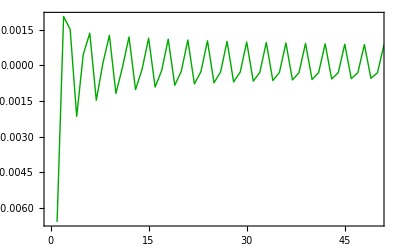

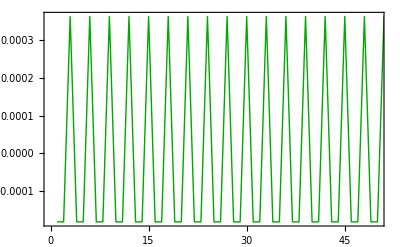

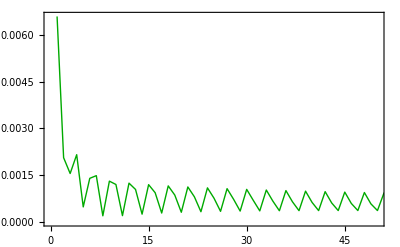

-Graphics-

```mathematica
(*GraphReGR=*)Real3l=ListPlot[{Table[{n,Re[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}](*,Table[{n,fr1[n]},{n,1,91,1}],Table[{n,-fr1[n]},{n,1,91,1}],rdata1*)},PlotRange->{{0,50},All},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Darker[Green],Thick}, {Gray,Dashed},{Gray,Dashed},Gray},Joined->{True,True,True,False}]

(*GraphImGR=*)
Imag3l=ListPlot[{Table[{n,Im[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}](*,Table[{n,fi1[n]},{n,1,91,1}],Table[{n,-fi1[n]},{n,1,91,1}],idata1*)},PlotRange->{{0,50},All},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Darker[Green],Thick}, {Gray,Dashed},{Gray,Dashed},Gray},Joined->{True,True,True,False},Joined->{True,True,True,True,False}]

(*GraphAbsGR=*)
Abs3l=ListPlot[{Table[{n,Abs[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}](*,Table[{n,f1[n]},{n,1,91,1}],data1*)},PlotRange->{{0,50},All},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Darker[Green],Thick}, {Gray,Dashed},Gray},Joined->{True,True,False}]

(*GraphLogAbsGR=*)
Abs3lLog=ListLogLogPlot[{(*Table[{n,Abs[G[δA,n Norm[ap],θ⟦1⟧,xx,yy,αα,ββ]]},{n,1,91,1}],*)Table[{n,f1[n]},{n,1,91,1}],data1},PlotRange->{{10,91},{0.0005,0.0015}},Frame->True,LabelStyle->Directive[Bold, Medium],PlotStyle->{{Darker[Green],Thick},Darker[Green],Black},Joined->{(*True,*)True,False},PlotMarkers->{None,"○"}]
```

#### Comparison

```mathematica
{Eps[xx1,yy1],Eps[xx2,yy2],Eps[xx3,yy3]}
```

{10.5625,10.5625,10.5625}

```mathematica
{{xx1,yy1},{Aabs1,γabs1}}
{{xx2,yy2},{Aabs2,γabs2}}
{{xx3,yy3},{Aabs3,γabs3}}
{{xxM,yyM},{AabsM,γabsM}}
(*GraphicsGrid[{{Abs1l,Abs2l,Abs3l},{Real1l,Real2l,Real3l},{Imag1l,Imag2l,Imag3l}},ImageSize->{850,500}]*)
```

{{-0.381051,0.06},{0.0132781,0.907228}}

{{-0.334863,0.},{0.00418203,0.369958}}

{{0.34641,-0.01},{0.00215104,0.214666}}

{{-0.311769,0.11},{0.000121058,0.885598}}

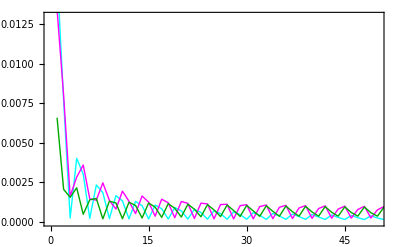

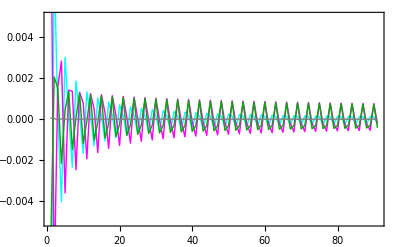

-Graphics-

```mathematica
Show[{Abs1l,Abs2l,Abs3l(*,AbsMl*)},PlotRange->{{0,50}, {0,0.013}}]
Show[{Real1l,Real2l,Real3l,RealMl},PlotRange-> {-0.005,0.005}]
Show[{Abs1lLog,Abs2lLog,Abs3lLog(*,AbsMlLog*)},ImageSize-> {200,120}]
(*Show[{Imag1l,Imag2l}(*,PlotRange-> {-0.008,0.008}*)]*)
```

#### Graphics for π/6

```mathematica
LogA1dri1=Table[{A1d1⟦i,1⟧,A1d1⟦i,2⟧,Log[10,A1dr1⟦i,3⟧/A1di1⟦i,3⟧]},{i,Length[A1d1]}];
LogA1ari1=Table[{A1a1⟦i,1⟧,A1a1⟦i,2⟧,Log[10,A1ar1⟦i,3⟧/A1ai1⟦i,3⟧]},{i,Length[A1a1]}];
LogA11=Join[LogA1dri1,LogA1ari1];
A1d1Norm=Table[{A1d1⟦i,1⟧,A1d1⟦i,2⟧,A1d1⟦i,3⟧*es},{i,Length[A1d1]}];
A1a1Norm=Table[{A1a1⟦i,1⟧,A1a1⟦i,2⟧,A1a1⟦i,3⟧*er},{i,Length[A1a1]}];
LogA1d1Norm=Table[{A1d1⟦i,1⟧,A1d1⟦i,2⟧,Log10[A1d1⟦i,3⟧]},{i,Length[A1d1]}];
LogA1a1Norm=Table[{A1a1⟦i,1⟧,A1a1⟦i,2⟧,Log10[A1a1⟦i,3⟧]},{i,Length[A1a1]}];
A11Norm=Join[A1d1Norm,A1a1Norm];A11Norm⟦All,3⟧=A11Norm⟦All,3⟧/Max[A11Norm⟦All,3⟧];
LogA11Norm=Join[LogA1d1Norm,LogA1a1Norm];
A11=Join[A1d1,A1a1];
γ11=Join[γ1d1,γ1a1];

cfγ=Blend[{{1,White},{0.85,LightRed},{0.4,Red},{Max[0,Min[γ11⟦All,3⟧]],Darker[Red]}},#]&;
cfA=Blend[{{0,White},{0.1(*Mean[A11Norm⟦All,3⟧]*),Yellow},{0.4,Red},{1,Darker[Red]}},#]&;
cfLogA=Blend[{(*{Min[LogA11Norm⟦All,3⟧],Darker[Blue]},*){-3,Blue},{0,White},{Max[LogA11Norm⟦All,3⟧],Red}},#]&;
cfAri=Blend[{(*{Min[LogA11⟦All,3⟧],Blue},*){0,White},{0.5Max[LogA11⟦All,3⟧],LightRed},{Max[LogA11⟦All,3⟧],Red}},#]&;
```

```mathematica
γGraph=ListDensityPlot[γ11,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfγ,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameTicksStyle->Black];
AGraph=ListDensityPlot[A11Norm,PlotRange->{0,2},PlotLegends->BarLegend[{cfA,{0,0.4}}],ColorFunction->cfA,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameTicksStyle->Black];
LAGraph=ListDensityPlot[LogA11Norm,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfLogA,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameTicksStyle->Black];

LogAGraph=ListDensityPlot[LogA11,PlotRange->All,PlotLegends->Automatic,ColorFunction->cfAri,ColorFunctionScaling->False,LabelStyle->Directive[Bold, Medium],Frame->{{True,None},{True,None}},FrameTicksStyle->Black];
```

```mathematica
GraphicsGrid[{{γGraph,AGraph,LogAGraph}},ImageSize->{950,250}]
GraphicsGrid[{{γGraph,LAGraph,LogAGraph}},ImageSize->{950,250}];
Export["GammaGxx-030.pdf",Show[γGraph,ListPlot[{{{xx1,yy1}},{{xx2,yy2}},{{xx3,yy3}}},PlotStyle->{{Thick,Cyan},{Thick,Magenta},{Thick,Green}}]]];
Export["AmpGxx-030.pdf",Show[AGraph,ListPlot[{{{xx1,yy1}},{{xx2,yy2}},{{xx3,yy3}}},PlotStyle->{{Thick,Cyan},{Thick,Magenta},{Thick,Green}}]]]; 
Export["RatioReImGxx-030.pdf",Show[LogAGraph,ListPlot[{{{xx1,yy1}},{{xx2,yy2}},{{xx3,yy3}}},PlotStyle->{{Thick,Cyan},{Thick,Magenta},{Thick,Green}}]]];
```

-Graphics-

## γ and A in line segments

Here, we analize the trade-off between range and strength of the interaction in a linear segments

### Mesh in linear segments

```mathematica
r1=0.5 a{-Cos[π/6],Sin[π/6]}
r2={xx2,yy2}
r3={0.3575,0.3575}
r4={0,0}
xi=(-r1⟦2⟧+r1⟦1⟧(r2⟦2⟧-r1⟦2⟧)/(r2⟦1⟧-r1⟦1⟧))/((r2⟦2⟧-r1⟦2⟧)/(r2⟦1⟧-r1⟦1⟧)-r3⟦2⟧/r3⟦1⟧)
yi=(r3⟦2⟧/r3⟦1⟧)xi
```

{-0.433013,0.25}

{-0.311769,0.11}

{0.3575,0.3575}

{0,0}

-0.116025

-0.116025

```mathematica
nx=100;
xP=1/Sqrt[3]{-1,0};xO={0,0};xQ=1/Sqrt[3]{Cos[π/3],Sin[π/3]};
(*xQ=0.5{-Cos[π/6],Sin[π/6]};xO={xi,yi};xP={0.3575,0.3575};*)
xPO=Table[N[Join[{Norm[xO-xP]i/(nx+1)},(xO-xP)i/(nx+1)+xP]],{i,0,nx+1}];
xOQ=Table[N[Join[{Norm[xO-xP]+N[Norm[xQ-xO]]i/(nx+1)},(xQ-xO)i/(nx+1)+xO]],{i,nx+1}];
xQP=Table[N[Join[{Norm[xO-xP]+N[Norm[xQ-xO]]+N[Norm[xP-xQ]]i/(nx+1)},(xP-xQ)i/(nx+1)+xQ]],{i,nx+1}];
Xs=Join[xPO,xOQ,xQP];
{Length[Xs],Length[xPO],Length[xOQ]}
{Xs⟦1⟧,Xs⟦102⟧}
Position[Table[Norm[xs],{xs,Xs⟦All,2;;3⟧}],Min[Table[Norm[xs],{xs,Xs⟦All,2;;3⟧}]]]
Xs⟦141⟧
```

{304,102,101}

{{0.,-0.57735,0.},{0.57735,0.,0.}}

{{102}}

{0.800288,0.111469,0.193069}

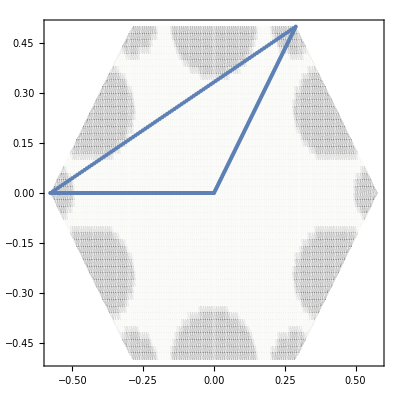

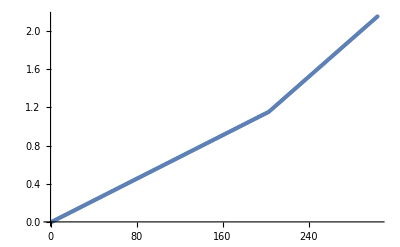

```mathematica
Show[EpsGrap,ListPlot[Xs⟦All,2;;3⟧]]
ListPlot[Xs⟦All,1⟧]
```

### Fit in the linear segments

```mathematica
αα=1;ββ=1;θ={π/6,π/2,5π/6};
γ1d1s={};A1d1s={};Rsq1d1s={};
```

```mathematica
TdieGxx0=AbsoluteTime[]; 
Do[tγ0=AbsoluteTime[];
{xx,yy}=xs⟦2;;3⟧;
{Fit1,Fit2,Fit3}=PowerFit[xx,yy,αα,ββ];

AppendTo[γ1d1s,{xs⟦1⟧,Fit1⟦1,2⟧}];AppendTo[A1d1s,{xs⟦1⟧,Eps[xx,yy]Fit1⟦1,1⟧}];AppendTo[Rsq1d1s,{xs⟦1⟧,Fit1⟦1,3⟧}];
,{xs,Xs}]
TdieGxx=AbsoluteTime[]-TdieGxx0
```

19.202738

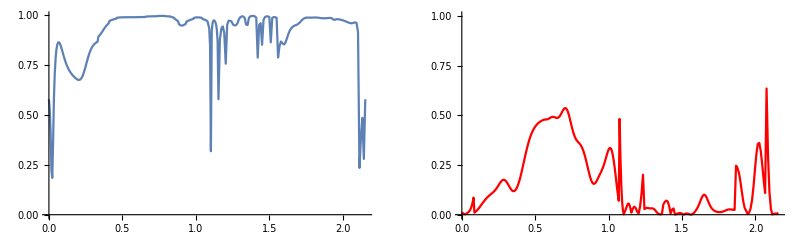

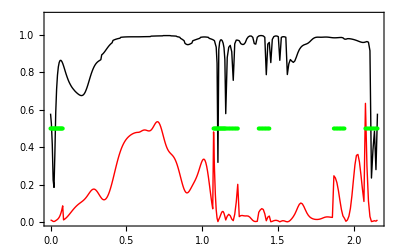

```mathematica
GraphicsGrid[{{γsGraph=ListPlot[γ1d1s,PlotRange->All,Joined->True],AsGraph=ListPlot[A1d1s,PlotRange->{0,1},Joined->True,PlotStyle->Red]}}]
ListPlot[{γ1d1s,A1d1s,Table[{xs⟦1⟧,0.5Eps[xs⟦2⟧,xs⟦3⟧]},{xs,Xs}]},PlotRange->{0,1.1},Joined->{True,True,False},LabelStyle->Directive[Large,(FontFamily->"Times")],Frame-> True,FrameTicks->{{True,None},{True,None}},PlotStyle->{{Black,Thick},{Red,Thick},{Green}}]
```

```mathematica
AbsGxx11lNorR001=Table[{A1d1s⟦j,1⟧, A1d1s⟦j,2⟧/1^γ1d1s⟦j,2⟧(*/Max[A1d1s⟦All,2⟧/1^γ1d1s⟦All,2⟧]*)},{j,Length[A1d1s]}];
AbsGxx11lNorR030=Table[{A1d1s⟦j,1⟧, 30A1d1s⟦j,2⟧/30^γ1d1s⟦j,2⟧(*/Max[A1d1s⟦All,2⟧/10^γ1d1s⟦All,2⟧]*)},{j,Length[A1d1s]}];
AbsGxx11lNorR300=Table[{A1d1s⟦j,1⟧,300 A1d1s⟦j,2⟧/300^γ1d1s⟦j,2⟧(*/Max[A1d1s⟦All,2⟧/100^γ1d1s⟦All,2⟧]*)},{j,Length[A1d1s]}];
```

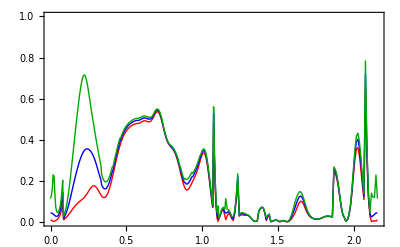

```mathematica
ListPlot[{AbsGxx11lNorR001,AbsGxx11lNorR010,AbsGxx11lNorR100},Joined->True,PlotRange->{0,1},LabelStyle->Directive[Large,(FontFamily->"Times")],Frame-> True,PlotStyle->{{Red,Thick},{Blue,Thick},{Darker[Green],Thick}}]
```